```mathematica
β[ω_,δ_,t_,ϵ_]:=
β[ω,δ,t,ϵ]=ReplacePart[(ω+ⅈ*δ-ϵ)IdentityMatrix[14],Join[Table[{i,i-1},{i,Range[2,14,1]}],Table[{i,i+1},{i,Range[1,14,1]}],Table[{2n-1,14-2n+2},{n,4}],Table[{14-2n+2,2n-1},{n,3}]]->-t]
```

```mathematica
T1[t_]:=T1[t]=ReplacePart[0*IdentityMatrix[14],Table[{2n,14-2n+1},{n,3}]->t]
```

```mathematica
TT[t_]:=ReplacePart[0*IdentityMatrix[14],Table[{2n,2n},{n,3}]->t]
```

```mathematica
LEFT=Table[ToExpression[Import["/home/shardulmukim/PhD/fwi/AGNR/7AGNR/Leads/lead_"<>ToString[ω]<>".dat"]],{ω,Range[0,3,0.01]}]
```

{{{0.-0.0000823223 ⅈ,-0.573223+0. ⅈ,0.+0.000025 ⅈ,0.25+0. ⅈ,0.-2.8033×10^-13 ⅈ,-0.0732233+0. ⅈ,0.-7.32233×10^-6 ⅈ,0.0732233+0. ⅈ,0.+0.0000146447 ⅈ,-0.176777+0. ⅈ,0.-0.0000323223 ⅈ,0.323223+0. ⅈ,0.+0.0000396447 ⅈ,-0.426777+0. ⅈ},12,{1}},299,{1}}
 |  |  |  |

```mathematica
g[ω_,δ_,t_,ϵ_]:= Inverse[β[ω,δ,t,ϵ]]
```

```mathematica
SR[ω_,δ_,t_,ϵ_]:=SR[ω,δ,t,ϵ]=Inverse[IdentityMatrix[14]-g[ω,δ,t,ϵ].ConjugateTranspose[T1[t]].LEFT[[ω*100+1]].T1[t]].g[ω,δ,t,ϵ]
```

```mathematica
SL[ω_,δ_,t_,ϵ_]:=SL[ω,δ,t,ϵ]=Inverse[IdentityMatrix[14]-g[ω,δ,t,ϵ].ConjugateTranspose[T1[t]].LEFT[[ω*100+1]].T1[t]].g[ω,δ,t,ϵ]
```

```mathematica
IL[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[14]-SL[ω,δ,t,ϵ].TT[t].SR[ω,δ,t,ϵ].TT[t]].SL[ω,δ,t,ϵ]
```

```mathematica
IR[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[14]-SR[ω,δ,t,ϵ].TT[t].SL[ω,δ,t,ϵ].TT[t]].SR[ω,δ,t,ϵ]
```

```mathematica
gdd[ω_,δ_,t_,ϵ_]:= IL[ω,δ,t,ϵ]-ConjugateTranspose[IL[ω,δ,t,ϵ]]
```

```mathematica
grr[ω_,δ_,t_,ϵ_]:= IR[ω,δ,t,ϵ]-ConjugateTranspose[IR[ω,δ,t,ϵ]]
```

```mathematica
Gnonlocal[ω_,δ_,t_,ϵ_]:= SR[ω,δ,t,ϵ].TT[t].IL[ω,δ,t,ϵ]
```

```mathematica
GNON[ω_,δ_,t_,ϵ_]:= Gnonlocal[ω,δ,t,ϵ]-ConjugateTranspose[Gnonlocal[ω,δ,t,ϵ]]
```

```mathematica
tr[ω_,δ_,t_,ϵ_]:= Abs[Tr[gdd[ω,δ,t,ϵ].TT[t].grr[ω,δ,t,ϵ].TT[t]-TT[t].GNON[ω,δ,t,ϵ].TT[t].GNON[ω,δ,t,ϵ]]]
```

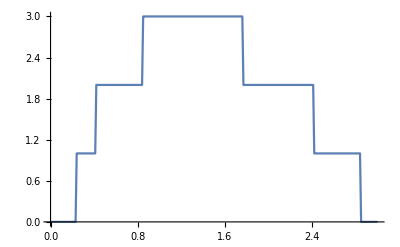

```mathematica
ListLinePlot[Table[{ω,tr[ω,0.0001,1,0]},{ω,0,3,0.01}]]
```

```mathematica
pris=Table[{ω,tr[ω,0.0001,1,0]},{ω,0,3,0.01}]
```

{{0.,2.8×10^-7},{0.01,2.8081×10^-7},{0.02,2.83264×10^-7},{0.03,2.87439×10^-7},{0.04,2.93463×10^-7},{0.05,3.01536×10^-7},{0.06,3.11935×10^-7},{0.07,3.25045×10^-7},{0.08,3.41391×10^-7},{0.09,3.61694×10^-7},{0.1,3.86954×10^-7},{0.11,4.18578×10^-7},{0.12,4.58598×10^-7},{0.13,5.10023×10^-7},{0.14,5.77474×10^-7},{0.15,6.68349×10^-7},{0.16,7.95126×10^-7},{0.17,9.803×10^-7},{0.18,1.26801×10^-6},{0.19,1.75544×10^-6},{0.2,2.69447×10^-6},{0.21,4.92698×10^-6},{0.22,0.0000129427},{0.23,0.000120119},{0.24,0.999916},{0.25,0.999991},{0.26,0.999997},{0.27,0.999999},{0.28,0.999999},{0.29,1.},{0.3,1.},{0.31,1.},{0.32,1.},{0.33,1.},{0.34,1.},{0.35,1.},{0.36,1.},{0.37,1.},{0.38,1.},{0.39,1.},{0.4,1.00001},{0.41,1.00014},{0.42,1.99993},{0.43,1.99999},{0.44,2.},{0.45,2.},{0.46,2.},{0.47,2.},{0.48,2.},{0.49,2.},{0.5,2.},{0.51,2.},{0.52,2.},{0.53,2.},{0.54,2.},{0.55,2.},{0.56,2.},{0.57,2.},{0.58,2.},{0.59,2.},{0.6,2.},{0.61,2.},{0.62,2.},{0.63,2.},{0.64,2.},{0.65,2.},{0.66,2.},{0.67,2.},{0.68,2.},{0.69,2.},{0.7,2.},{0.71,2.},{0.72,2.},{0.73,2.},{0.74,2.},{0.75,2.},{0.76,2.},{0.77,2.},{0.78,2.},{0.79,2.},{0.8,2.},{0.81,2.},{0.82,2.},{0.83,2.00001},{0.84,2.00004},{0.85,2.9995},{0.86,2.99998},{0.87,2.99999},{0.88,3.},{0.89,3.},{0.9,3.},{0.91,3.},{0.92,3.},{0.93,3.},{0.94,3.},{0.95,3.},{0.96,3.},{0.97,3.},{0.98,3.},{0.99,3.},{1.,3.},{1.01,3.},{1.02,3.},{1.03,3.},{1.04,3.},{1.05,3.},{1.06,3.},{1.07,3.},{1.08,3.},{1.09,3.},{1.1,3.},{1.11,3.},{1.12,3.},{1.13,3.},{1.14,3.},{1.15,3.},{1.16,3.},{1.17,3.},{1.18,3.},{1.19,3.},{1.2,3.},{1.21,3.},{1.22,3.},{1.23,3.},{1.24,3.},{1.25,3.},{1.26,3.},{1.27,3.},{1.28,3.},{1.29,3.},{1.3,3.},{1.31,3.},{1.32,3.},{1.33,3.},{1.34,3.},{1.35,3.},{1.36,3.},{1.37,3.},{1.38,3.},{1.39,3.},{1.4,3.},{1.41,3.},{1.42,3.},{1.43,3.},{1.44,3.},{1.45,3.},{1.46,3.},{1.47,3.},{1.48,3.},{1.49,3.},{1.5,3.},{1.51,3.},{1.52,3.},{1.53,3.},{1.54,3.},{1.55,3.},{1.56,3.},{1.57,3.},{1.58,3.},{1.59,3.},{1.6,3.},{1.61,3.},{1.62,3.},{1.63,3.},{1.64,3.},{1.65,3.},{1.66,3.},{1.67,3.},{1.68,3.},{1.69,3.},{1.7,3.},{1.71,3.},{1.72,3.},{1.73,3.},{1.74,3.},{1.75,2.99999},{1.76,2.99991},{1.77,2.00012},{1.78,2.00001},{1.79,2.},{1.8,2.},{1.81,2.},{1.82,2.},{1.83,2.},{1.84,2.},{1.85,2.},{1.86,2.},{1.87,2.},{1.88,2.},{1.89,2.},{1.9,2.},{1.91,2.},{1.92,2.},{1.93,2.},{1.94,2.},{1.95,2.},{1.96,2.},{1.97,2.},{1.98,2.},{1.99,2.},{2.,2.},{2.01,2.},{2.02,2.},{2.03,2.},{2.04,2.},{2.05,2.},{2.06,2.},{2.07,2.},{2.08,2.},{2.09,2.},{2.1,2.},{2.11,2.},{2.12,2.},{2.13,2.},{2.14,2.},{2.15,2.},{2.16,2.},{2.17,2.},{2.18,2.},{2.19,2.},{2.2,2.},{2.21,2.},{2.22,2.},{2.23,2.},{2.24,2.},{2.25,2.},{2.26,2.},{2.27,2.},{2.28,2.},{2.29,2.},{2.3,2.},{2.31,2.},{2.32,2.},{2.33,2.},{2.34,2.},{2.35,2.},{2.36,2.},{2.37,2.},{2.38,2.},{2.39,2.},{2.4,1.99999},{2.41,1.99986},{2.42,1.00007},{2.43,1.00001},{2.44,1.},{2.45,1.},{2.46,1.},{2.47,1.},{2.48,1.},{2.49,1.},{2.5,1.},{2.51,1.},{2.52,1.},{2.53,1.},{2.54,1.},{2.55,1.},{2.56,1.},{2.57,1.},{2.58,1.},{2.59,1.},{2.6,1.},{2.61,1.},{2.62,1.},{2.63,1.},{2.64,1.},{2.65,1.},{2.66,1.},{2.67,1.},{2.68,1.},{2.69,1.},{2.7,1.},{2.71,1.},{2.72,1.},{2.73,1.},{2.74,1.},{2.75,1.},{2.76,1.},{2.77,1.},{2.78,0.999999},{2.79,0.999999},{2.8,0.999999},{2.81,0.999998},{2.82,0.999997},{2.83,0.999992},{2.84,0.999958},{2.85,0.000496198},{2.86,0.0000165305},{2.87,4.97473×10^-6},{2.88,2.35363×10^-6},{2.89,1.36412×10^-6},{2.9,8.87821×10^-7},{2.91,6.22951×10^-7},{2.92,4.6079×10^-7},{2.93,3.54437×10^-7},{2.94,2.8098×10^-7},{2.95,2.28152×10^-7},{2.96,1.88907×10^-7},{2.97,1.58966×10^-7},{2.98,1.35611×10^-7},{2.99,1.17044×10^-7},{3.,1.02043×10^-7}}

```mathematica
RandomSample[Join[RandomSample[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp14,imp13},7],(*RandomSample[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp14,imp13}],RandomSample[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp14,imp13}],RandomSample[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp14,imp13}],RandomSample[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp14,imp13}],*)Table[imp,43]]]
```

{imp,imp,imp,imp,imp,imp,imp13,imp10,imp,imp,imp,imp,imp,imp,imp,imp7,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp1,imp,imp6,imp,imp,imp,imp8,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp2,imp}

```mathematica
m5[ω_,ϵ1_]:=Module[{Tin=T1[1],T=TT[1],,μ1=RandomInteger[{1,14}], μ2=RandomInteger[{1,14}], μ3=RandomInteger[{1,14}], μ4=RandomInteger[{1,14}],μ5=RandomInteger[{1,14}], μ6=RandomInteger[{1,14}], μ7=RandomInteger[{1,14}],μ8=RandomInteger[{1,14}], μ9=RandomInteger[{1,14}], μ10=RandomInteger[{1,14}], μ11=RandomInteger[{1,14}],μ12=RandomInteger[{1,14}], μ13=RandomInteger[{1,14}], μ14=RandomInteger[{1,14}], μ15=RandomInteger[{8,14}],μ16=RandomInteger[{8,14}]},
tra1:=Module[{},
b=Module[{imp1:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ1,μ1}}->ω+ⅈ*0.0001-ϵ1]]],
imp2:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ2,μ2}}->ω+ⅈ*0.0001-ϵ1]]],
imp3:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ3,μ3}}->ω+ⅈ*0.0001-ϵ1]]],
imp4:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ4,μ4}}->ω+ⅈ*0.0001-ϵ1]]],
imp5:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ5,μ5}}->ω+ⅈ*0.0001-ϵ1]]],
imp6:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ6,μ6}}->ω+ⅈ*0.0001-ϵ1]]],
imp7:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ7,μ7}}->ω+ⅈ*0.0001-ϵ1]]],
imp8:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ8,μ8}}->ω+ⅈ*0.0001-ϵ1]]],
imp9:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ9,μ9}}->ω+ⅈ*0.0001-ϵ1]]],
imp10:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ10,μ10}}->ω+ⅈ*0.0001-ϵ1]]],
imp11:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ11,μ11}}->ω+ⅈ*0.0001-ϵ1]]],
imp12:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ12,μ12}}->ω+ⅈ*0.0001-ϵ1]]],
imp13:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ13,μ13}}->ω+ⅈ*0.0001-ϵ1]]],
imp14:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ14,μ14}}->ω+ⅈ*0.0001-ϵ1]]],
imp:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{14,14}}->ω+ⅈ*0.0001-0]]]},
lista={RandomSample[{imp1,imp2,imp,imp,imp(*,imp,imp9,imp,imp,imp,imp,imp,imp,imp,imp,imp7,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp1,imp,imp6,imp,imp,imp,imp8,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp2,imp*)}]};
sl1= Module[{J=SL[ω,0.0001,1,0]},Do[J=Inverse[IdentityMatrix[14]-lista[[1,ζ]].ConjugateTranspose[Tin].J.Tin].lista[[1,ζ]],{ζ,1,5}];J=J];Il1:=Inverse[IdentityMatrix[14]-sl1.T.SR[ω,0.0001,1,0].T].sl1;
Ir1:=Inverse[IdentityMatrix[14]-SR[ω,0.0001,1,0].T.sl1.T].SR[ω,0.0001,1,0];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,0.0001,1,0].T.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];If[Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]>tr[ω,0.0001,1,0],tr[ω,0.0001,1,0],Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]]];
b];
{Log[tra1],tra1}]
```

```mathematica
Table[{ω,Mean[Table[m5[ω,0.5],2000]]},{ω,Range[0,3,0.01]}]
```

{{0.,{-15.1901,2.62268×10^-7}},{0.01,{-15.3772,2.33653×10^-7}},{0.02,{-15.3338,2.45611×10^-7}},{0.03,{-15.2551,2.56423×10^-7}},{0.04,{-15.2078,2.65511×10^-7}},{0.05,{-15.1881,2.76463×10^-7}},{0.06,{-15.1199,2.8272×10^-7}},{0.07,{-15.0763,3.04111×10^-7}},{0.08,{-15.0048,3.17042×10^-7}},{0.09,{-14.9674,3.33717×10^-7}},{0.1,{-14.9042,3.59705×10^-7}},{0.11,{-14.8324,3.88896×10^-7}},{0.12,{-14.7133,4.32471×10^-7}},{0.13,{-14.5692,4.83265×10^-7}},{0.14,{-14.4213,5.5043×10^-7}},{0.15,{-14.2943,6.40909×10^-7}},{0.16,{-14.1001,7.7041×10^-7}},{0.17,{-13.8926,9.50031×10^-7}},{0.18,{-13.6279,1.23859×10^-6}},{0.19,{-13.2907,1.71727×10^-6}},{0.2,{-12.8586,2.64156×10^-6}},{0.21,{-12.2836,4.82167×10^-6}},{0.22,{-11.3059,0.0000126137}},{0.23,{-9.12919,0.00011477}},{0.24,{-0.610148,0.589838}},{0.25,{-0.227277,0.806998}},{0.26,{-0.134801,0.878071}},{0.27,{-0.0962133,0.911833}},{0.28,{-0.0755421,0.929254}},{0.29,{-0.0655996,0.941006}},{0.3,{-0.0545226,0.948865}},{0.31,{-0.0474264,0.952944}},{0.32,{-0.0470581,0.955141}},{0.33,{-0.0445799,0.95798}},{0.34,{-0.0449756,0.956948}},{0.35,{-0.0429807,0.958962}},{0.36,{-0.0448988,0.954498}},{0.37,{-0.0478705,0.952233}},{0.38,{-0.0527465,0.949361}},{0.39,{-0.067126,0.936579}},{0.4,{-0.097994,0.907833}},{0.41,{-0.258553,0.789399}},{0.42,{0.122414,1.20662}},{0.43,{0.453733,1.58649}},{0.44,{0.535745,1.71417}},{0.45,{0.572739,1.78343}},{0.46,{0.599881,1.82201}},{0.47,{0.611839,1.84494}},{0.48,{0.622251,1.86548}},{0.49,{0.631451,1.88117}},{0.5,{0.637333,1.89156}},{0.51,{0.641191,1.89841}},{0.52,{0.643486,1.9036}},{0.53,{0.647429,1.9116}},{0.54,{0.648668,1.91423}},{0.55,{0.650535,1.9184}},{0.56,{0.654375,1.92288}},{0.57,{0.65524,1.92532}},{0.58,{0.656121,1.92704}},{0.59,{0.6566,1.929}},{0.6,{0.658155,1.93059}},{0.61,{0.659205,1.93226}},{0.62,{0.659531,1.93379}},{0.63,{0.659966,1.93586}},{0.64,{0.659514,1.93582}},{0.65,{0.660513,1.93809}},{0.66,{0.661853,1.93871}},{0.67,{0.661182,1.93894}},{0.68,{0.662359,1.93891}},{0.69,{0.662551,1.9395}},{0.7,{0.662941,1.94088}},{0.71,{0.662789,1.94108}},{0.72,{0.663323,1.94141}},{0.73,{0.664145,1.94314}},{0.74,{0.663105,1.94185}},{0.75,{0.663858,1.94232}},{0.76,{0.662775,1.9415}},{0.77,{0.663714,1.94135}},{0.78,{0.662817,1.94056}},{0.79,{0.662025,1.93756}},{0.8,{0.659526,1.93417}},{0.81,{0.655986,1.92845}},{0.82,{0.650847,1.91778}},{0.83,{0.637209,1.89394}},{0.84,{0.593793,1.81157}},{0.85,{0.26632,1.49435}},{0.86,{0.829867,2.32079}},{0.87,{0.926379,2.53813}},{0.88,{0.969932,2.6546}},{0.89,{0.997166,2.71481}},{0.9,{1.01407,2.76134}},{0.91,{1.02365,2.78776}},{0.92,{1.03166,2.80801}},{0.93,{1.03895,2.82825}},{0.94,{1.04235,2.83816}},{0.95,{1.04902,2.8572}},{0.96,{1.05281,2.86895}},{0.97,{1.05553,2.87652}},{0.98,{1.05913,2.88483}},{0.99,{1.06041,2.88853}},{1.,{1.06237,2.8951}},{1.01,{1.06309,2.89583}},{1.02,{1.05951,2.88662}},{1.03,{1.04623,2.84816}},{1.04,{1.00349,2.7319}},{1.05,{0.872049,2.40634}},{1.06,{0.584943,1.87389}},{1.07,{0.594787,1.87921}},{1.08,{0.772867,2.19087}},{1.09,{0.872828,2.4092}},{1.1,{0.925338,2.52991}},{1.11,{0.95507,2.6055}},{1.12,{0.974901,2.65338}},{1.13,{0.988175,2.68498}},{1.14,{0.996228,2.71077}},{1.15,{1.00348,2.73117}},{1.16,{1.00791,2.74332}},{1.17,{1.01255,2.75713}},{1.18,{1.01576,2.76389}},{1.19,{1.01945,2.76886}},{1.2,{1.02023,2.77585}},{1.21,{1.0223,2.78034}},{1.22,{1.02393,2.78341}},{1.23,{1.0254,2.78763}},{1.24,{1.0273,2.7919}},{1.25,{1.0277,2.79394}},{1.26,{1.02784,2.79727}},{1.27,{1.02843,2.79796}},{1.28,{1.02861,2.79869}},{1.29,{1.02816,2.79702}},{1.3,{1.02961,2.80118}},{1.31,{1.03001,2.80264}},{1.32,{1.02918,2.80066}},{1.33,{1.02957,2.80178}},{1.34,{1.02969,2.79962}},{1.35,{1.0289,2.79752}},{1.36,{1.02899,2.79439}},{1.37,{1.02803,2.79782}},{1.38,{1.02875,2.79515}},{1.39,{1.02741,2.79483}},{1.4,{1.02694,2.7942}},{1.41,{1.02597,2.7947}},{1.42,{1.02674,2.79287}},{1.43,{1.02559,2.78998}},{1.44,{1.02552,2.78961}},{1.45,{1.02471,2.78904}},{1.46,{1.02298,2.78303}},{1.47,{1.02201,2.77957}},{1.48,{1.02134,2.77662}},{1.49,{1.02044,2.77546}},{1.5,{1.01894,2.77118}},{1.51,{1.01833,2.7694}},{1.52,{1.01635,2.76258}},{1.53,{1.01442,2.75932}},{1.54,{1.01189,2.75288}},{1.55,{1.01066,2.74893}},{1.56,{1.00971,2.74192}},{1.57,{1.00547,2.73423}},{1.58,{1.00433,2.72797}},{1.59,{1.00234,2.72583}},{1.6,{0.997136,2.71385}},{1.61,{0.992713,2.70297}},{1.62,{0.990283,2.6902}},{1.63,{0.985376,2.68086}},{1.64,{0.979915,2.66313}},{1.65,{0.973875,2.64876}},{1.66,{0.965849,2.63276}},{1.67,{0.958284,2.61235}},{1.68,{0.950362,2.59146}},{1.69,{0.938003,2.55763}},{1.7,{0.924831,2.53088}},{1.71,{0.905725,2.47139}},{1.72,{0.876823,2.41471}},{1.73,{0.839403,2.3224}},{1.74,{0.770497,2.19066}},{1.75,{0.653743,1.9796}},{1.76,{0.135968,1.41893}},{1.77,{0.0871305,1.36386}},{1.78,{0.0432725,1.29391}},{1.79,{0.159701,1.38622}},{1.8,{0.284135,1.47448}},{1.81,{0.423294,1.63744}},{1.82,{0.51612,1.72595}},{1.83,{0.57572,1.78204}},{1.84,{0.597377,1.82468}},{1.85,{0.609059,1.84707}},{1.86,{0.619658,1.85704}},{1.87,{0.624161,1.86723}},{1.88,{0.628893,1.87133}},{1.89,{0.630542,1.87632}},{1.9,{0.632642,1.88276}},{1.91,{0.632309,1.88453}},{1.92,{0.635707,1.88935}},{1.93,{0.636399,1.88944}},{1.94,{0.636065,1.89021}},{1.95,{0.635959,1.89055}},{1.96,{0.638253,1.89267}},{1.97,{0.63735,1.89253}},{1.98,{0.638462,1.89395}},{1.99,{0.637194,1.8926}},{2.,{0.637286,1.89271}},{2.01,{0.636261,1.8902}},{2.02,{0.637273,1.89224}},{2.03,{0.635907,1.89126}},{2.04,{0.635647,1.88941}},{2.05,{0.634504,1.88771}},{2.06,{0.63443,1.88864}},{2.07,{0.63273,1.88449}},{2.08,{0.634293,1.8863}},{2.09,{0.631485,1.88183}},{2.1,{0.63305,1.88266}},{2.11,{0.630536,1.87964}},{2.12,{0.629774,1.87906}},{2.13,{0.628599,1.87676}},{2.14,{0.62724,1.8738}},{2.15,{0.628391,1.87413}},{2.16,{0.625012,1.87015}},{2.17,{0.625536,1.87009}},{2.18,{0.623088,1.86538}},{2.19,{0.621185,1.86137}},{2.2,{0.619254,1.86133}},{2.21,{0.617681,1.85518}},{2.22,{0.614777,1.84755}},{2.23,{0.614037,1.84524}},{2.24,{0.608787,1.8447}},{2.25,{0.605603,1.83561}},{2.26,{0.60356,1.82852}},{2.27,{0.5998,1.82219}},{2.28,{0.593935,1.81407}},{2.29,{0.591332,1.80967}},{2.3,{0.586265,1.80117}},{2.31,{0.578544,1.79134}},{2.32,{0.571321,1.7793}},{2.33,{0.562573,1.76124}},{2.34,{0.551696,1.7355}},{2.35,{0.538634,1.71736}},{2.36,{0.518808,1.69045}},{2.37,{0.495264,1.6479}},{2.38,{0.464464,1.60537}},{2.39,{0.416784,1.52427}},{2.4,{0.322469,1.39997}},{2.41,{-0.0768895,1.02531}},{2.42,{-0.531492,0.714342}},{2.43,{-0.556629,0.697025}},{2.44,{-0.521812,0.718002}},{2.45,{-0.374967,0.77974}},{2.46,{-0.229141,0.848243}},{2.47,{-0.144884,0.877892}},{2.48,{-0.116204,0.898166}},{2.49,{-0.097702,0.912228}},{2.5,{-0.0842694,0.920096}},{2.51,{-0.0798733,0.925926}},{2.52,{-0.0748662,0.928193}},{2.53,{-0.0718263,0.931513}},{2.54,{-0.0725671,0.933369}},{2.55,{-0.0709623,0.931829}},{2.56,{-0.0693736,0.934902}},{2.57,{-0.0682349,0.934911}},{2.58,{-0.0694258,0.933826}},{2.59,{-0.0709958,0.933902}},{2.6,{-0.0708288,0.930761}},{2.61,{-0.0739737,0.930366}},{2.62,{-0.0738672,0.929657}},{2.63,{-0.0752578,0.925107}},{2.64,{-0.0766382,0.924785}},{2.65,{-0.0837217,0.922297}},{2.66,{-0.0826016,0.92098}},{2.67,{-0.0864907,0.92038}},{2.68,{-0.0901304,0.915758}},{2.69,{-0.0954316,0.912824}},{2.7,{-0.101191,0.909123}},{2.71,{-0.104806,0.910228}},{2.72,{-0.108883,0.900868}},{2.73,{-0.112284,0.896809}},{2.74,{-0.126028,0.888661}},{2.75,{-0.136399,0.882045}},{2.76,{-0.137885,0.875339}},{2.77,{-0.15488,0.860769}},{2.78,{-0.185683,0.8424}},{2.79,{-0.204816,0.827392}},{2.8,{-0.241307,0.803989}},{2.81,{-0.27552,0.781112}},{2.82,{-0.335689,0.745906}},{2.83,{-0.448409,0.684073}},{2.84,{-0.706864,0.547787}},{2.85,{-8.31928,0.000324517}},{2.86,{-11.0946,0.0000156523}},{2.87,{-12.2934,4.79529×10^-6}},{2.88,{-13.0832,2.24626×10^-6}},{2.89,{-13.6164,1.29996×10^-6}},{2.9,{-14.091,8.15635×10^-7}},{2.91,{-14.427,5.75446×10^-7}},{2.92,{-14.7464,4.29435×10^-7}},{2.93,{-14.936,3.35603×10^-7}},{2.94,{-15.1406,2.70494×10^-7}},{2.95,{-15.3347,2.20084×10^-7}},{2.96,{-15.5155,1.83714×10^-7}},{2.97,{-15.6895,1.53197×10^-7}},{2.98,{-15.8721,1.29404×10^-7}},{2.99,{-16.1123,1.11483×10^-7}},{3.,{-16.2132,9.72285×10^-8}}}

```mathematica
Tally[{imp1,imp2,imp3,imp4,imp,imp,imp,imp,imp,imp}]
```

{{imp1,1},{imp2,1},{imp3,1},{imp4,1},{imp,6}}

```mathematica
m10[ω_,ϵ1_]:=Module[{Tin=T1[1],T=TT[1],,μ1=RandomInteger[{1,14}], μ2=RandomInteger[{1,14}], μ3=RandomInteger[{1,14}], μ4=RandomInteger[{1,14}],μ5=RandomInteger[{1,14}], μ6=RandomInteger[{1,14}], μ7=RandomInteger[{1,14}],μ8=RandomInteger[{1,14}], μ9=RandomInteger[{1,14}], μ10=RandomInteger[{1,14}], μ11=RandomInteger[{1,14}],μ12=RandomInteger[{1,14}], μ13=RandomInteger[{1,14}], μ14=RandomInteger[{1,14}], μ15=RandomInteger[{8,14}],μ16=RandomInteger[{8,14}]},
tra1:=Module[{},
b=Module[{imp1:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ1,μ1}}->ω+ⅈ*0.0001-ϵ1]]],
imp2:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ2,μ2}}->ω+ⅈ*0.0001-ϵ1]]],
imp3:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ3,μ3}}->ω+ⅈ*0.0001-ϵ1]]],
imp4:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ4,μ4}}->ω+ⅈ*0.0001-ϵ1]]],
imp5:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ5,μ5}}->ω+ⅈ*0.0001-ϵ1]]],
imp6:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ6,μ6}}->ω+ⅈ*0.0001-ϵ1]]],
imp7:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ7,μ7}}->ω+ⅈ*0.0001-ϵ1]]],
imp8:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ8,μ8}}->ω+ⅈ*0.0001-ϵ1]]],
imp9:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ9,μ9}}->ω+ⅈ*0.0001-ϵ1]]],
imp10:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ10,μ10}}->ω+ⅈ*0.0001-ϵ1]]],
imp11:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ11,μ11}}->ω+ⅈ*0.0001-ϵ1]]],
imp12:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ12,μ12}}->ω+ⅈ*0.0001-ϵ1]]],
imp13:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ13,μ13}}->ω+ⅈ*0.0001-ϵ1]]],
imp14:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ14,μ14}}->ω+ⅈ*0.0001-ϵ1]]],
imp:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{14,14}}->ω+ⅈ*0.0001-0]]]},
lista={RandomSample[{imp1,imp2,imp3,imp4,imp,imp,imp,imp,imp,imp(*,imp,imp,imp,imp,imp7,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp1,imp,imp6,imp,imp,imp,imp8,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp2,imp*)}]};
sl1= Module[{J=SL[ω,0.0001,1,0]},Do[J=Inverse[IdentityMatrix[14]-lista[[1,ζ]].ConjugateTranspose[Tin].J.Tin].lista[[1,ζ]],{ζ,1,10}];J=J];Il1:=Inverse[IdentityMatrix[14]-sl1.T.SR[ω,0.0001,1,0].T].sl1;
Ir1:=Inverse[IdentityMatrix[14]-SR[ω,0.0001,1,0].T.sl1.T].SR[ω,0.0001,1,0];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,0.0001,1,0].T.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];If[Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]>tr[ω,0.0001,1,0],tr[ω,0.0001,1,0],Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]]];
b];
{Log[tra1],tra1}]
Table[{ω,Mean[Table[m10[ω,0.5],2000]]},{ω,Range[0,3,0.01]}]
```

{{0.,{-15.1863,2.62447×10^-7}},{0.01,{-15.3671,2.42477×10^-7}},{0.02,{-15.2903,2.48665×10^-7}},{0.03,{-15.2402,2.6144×10^-7}},{0.04,{-15.2108,2.68903×10^-7}},{0.05,{-15.1675,2.79682×10^-7}},{0.06,{-15.114,2.90369×10^-7}},{0.07,{-15.0589,3.04759×10^-7}},{0.08,{-15.0016,3.20486×10^-7}},{0.09,{-14.9551,3.37962×10^-7}},{0.1,{-14.919,3.59777×10^-7}},{0.11,{-14.8197,3.92266×10^-7}},{0.12,{-14.7321,4.27304×10^-7}},{0.13,{-14.5921,4.7586×10^-7}},{0.14,{-14.4576,5.50022×10^-7}},{0.15,{-14.3112,6.40513×10^-7}},{0.16,{-14.1295,7.57914×10^-7}},{0.17,{-13.9189,9.34537×10^-7}},{0.18,{-13.6381,1.21584×10^-6}},{0.19,{-13.3186,1.68228×10^-6}},{0.2,{-12.893,2.57829×10^-6}},{0.21,{-12.2966,4.6892×10^-6}},{0.22,{-11.3535,0.0000122937}},{0.23,{-9.23238,0.000109603}},{0.24,{-1.65716,0.252793}},{0.25,{-0.606469,0.583961}},{0.26,{-0.283396,0.771739}},{0.27,{-0.157757,0.863079}},{0.28,{-0.117688,0.893492}},{0.29,{-0.103624,0.907694}},{0.3,{-0.0941024,0.9134}},{0.31,{-0.0810183,0.92495}},{0.32,{-0.0784047,0.925019}},{0.33,{-0.0733459,0.92995}},{0.34,{-0.071907,0.932851}},{0.35,{-0.0695,0.932569}},{0.36,{-0.0718443,0.933078}},{0.37,{-0.0705837,0.931835}},{0.38,{-0.0758506,0.927446}},{0.39,{-0.0902061,0.916917}},{0.4,{-0.122935,0.889147}},{0.41,{-0.276536,0.781136}},{0.42,{-0.527541,0.772509}},{0.43,{0.0705537,1.1611}},{0.44,{0.338022,1.43592}},{0.45,{0.442254,1.58702}},{0.46,{0.509045,1.67149}},{0.47,{0.537197,1.71989}},{0.48,{0.554374,1.74545}},{0.49,{0.571601,1.77981}},{0.5,{0.579756,1.79627}},{0.51,{0.590799,1.80738}},{0.52,{0.598446,1.81749}},{0.53,{0.603424,1.83112}},{0.54,{0.607687,1.83964}},{0.55,{0.612095,1.84383}},{0.56,{0.613667,1.84877}},{0.57,{0.618779,1.85872}},{0.58,{0.619929,1.86043}},{0.59,{0.623179,1.86423}},{0.6,{0.625733,1.8696}},{0.61,{0.626889,1.87136}},{0.62,{0.627688,1.87463}},{0.63,{0.629046,1.87779}},{0.64,{0.629921,1.88098}},{0.65,{0.6317,1.88036}},{0.66,{0.632306,1.883}},{0.67,{0.633566,1.88819}},{0.68,{0.633406,1.88881}},{0.69,{0.63363,1.88873}},{0.7,{0.636186,1.88967}},{0.71,{0.636341,1.89137}},{0.72,{0.637861,1.89245}},{0.73,{0.639272,1.89294}},{0.74,{0.638805,1.89674}},{0.75,{0.639087,1.89575}},{0.76,{0.639349,1.89558}},{0.77,{0.640662,1.89634}},{0.78,{0.639698,1.89437}},{0.79,{0.638863,1.89684}},{0.8,{0.636339,1.89184}},{0.81,{0.635985,1.88591}},{0.82,{0.629191,1.87606}},{0.83,{0.617562,1.85406}},{0.84,{0.57344,1.78355}},{0.85,{-0.00274454,1.19129}},{0.86,{0.486691,1.73916}},{0.87,{0.729757,2.12433}},{0.88,{0.83407,2.35688}},{0.89,{0.897826,2.47669}},{0.9,{0.926888,2.53895}},{0.91,{0.950834,2.60455}},{0.92,{0.964767,2.63144}},{0.93,{0.979051,2.6703}},{0.94,{0.991066,2.70048}},{0.95,{0.996302,2.71752}},{0.96,{1.00781,2.74783}},{0.97,{1.01305,2.75956}},{0.98,{1.01643,2.77008}},{0.99,{1.02445,2.78623}},{1.,{1.02842,2.79677}},{1.01,{1.02842,2.79861}},{1.02,{1.02029,2.77564}},{1.03,{0.998936,2.70996}},{1.04,{0.915666,2.49704}},{1.05,{0.665703,1.97026}},{1.06,{0.143486,1.27159}},{1.07,{0.112316,1.24271}},{1.08,{0.483336,1.67991}},{1.09,{0.673933,1.99259}},{1.1,{0.764808,2.16737}},{1.11,{0.823875,2.28963}},{1.12,{0.86376,2.37365}},{1.13,{0.883838,2.42737}},{1.14,{0.898962,2.46772}},{1.15,{0.914742,2.50014}},{1.16,{0.92372,2.52355}},{1.17,{0.931131,2.53835}},{1.18,{0.936343,2.55743}},{1.19,{0.943061,2.57268}},{1.2,{0.949062,2.59025}},{1.21,{0.950466,2.59304}},{1.22,{0.95463,2.59842}},{1.23,{0.955632,2.60485}},{1.24,{0.957442,2.60847}},{1.25,{0.959623,2.61}},{1.26,{0.960949,2.61331}},{1.27,{0.960519,2.61943}},{1.28,{0.96055,2.62256}},{1.29,{0.962898,2.62026}},{1.3,{0.96396,2.6215}},{1.31,{0.962627,2.62421}},{1.32,{0.962895,2.62019}},{1.33,{0.964361,2.62029}},{1.34,{0.964418,2.62279}},{1.35,{0.965548,2.62487}},{1.36,{0.962977,2.62712}},{1.37,{0.961765,2.6238}},{1.38,{0.96482,2.62296}},{1.39,{0.96249,2.6123}},{1.4,{0.959857,2.61709}},{1.41,{0.959044,2.61574}},{1.42,{0.958353,2.61256}},{1.43,{0.957016,2.60683}},{1.44,{0.95707,2.5992}},{1.45,{0.951912,2.60076}},{1.46,{0.951441,2.59431}},{1.47,{0.951201,2.58901}},{1.48,{0.94768,2.58579}},{1.49,{0.945859,2.57839}},{1.5,{0.944905,2.57755}},{1.51,{0.943825,2.5689}},{1.52,{0.939081,2.56005}},{1.53,{0.939172,2.55343}},{1.54,{0.932992,2.54338}},{1.55,{0.929667,2.53972}},{1.56,{0.925352,2.52696}},{1.57,{0.921149,2.51986}},{1.58,{0.918928,2.51642}},{1.59,{0.912704,2.50051}},{1.6,{0.906655,2.48433}},{1.61,{0.901866,2.46866}},{1.62,{0.890878,2.43737}},{1.63,{0.883363,2.41917}},{1.64,{0.874353,2.39852}},{1.65,{0.864562,2.38593}},{1.66,{0.851568,2.35625}},{1.67,{0.834668,2.3261}},{1.68,{0.823012,2.28842}},{1.69,{0.799453,2.23525}},{1.7,{0.77307,2.18672}},{1.71,{0.738917,2.11002}},{1.72,{0.690869,2.01992}},{1.73,{0.626542,1.90517}},{1.74,{0.515311,1.72203}},{1.75,{0.235823,1.42468}},{1.76,{-0.235573,1.02039}},{1.77,{-0.0408874,1.22553}},{1.78,{0.028657,1.26951}},{1.79,{0.0391712,1.23023}},{1.8,{0.0972071,1.29415}},{1.81,{0.283045,1.43132}},{1.82,{0.389411,1.55523}},{1.83,{0.490404,1.65674}},{1.84,{0.531326,1.70777}},{1.85,{0.545504,1.7385}},{1.86,{0.558137,1.7529}},{1.87,{0.566965,1.7683}},{1.88,{0.572669,1.77681}},{1.89,{0.577318,1.78295}},{1.9,{0.579745,1.78771}},{1.91,{0.58338,1.79418}},{1.92,{0.584897,1.79651}},{1.93,{0.586458,1.80106}},{1.94,{0.583646,1.80243}},{1.95,{0.589286,1.80658}},{1.96,{0.586455,1.80538}},{1.97,{0.588062,1.79897}},{1.98,{0.585952,1.80206}},{1.99,{0.585903,1.8004}},{2.,{0.586013,1.80025}},{2.01,{0.585743,1.80023}},{2.02,{0.586177,1.79732}},{2.03,{0.584084,1.79455}},{2.04,{0.585167,1.79441}},{2.05,{0.581201,1.79405}},{2.06,{0.582756,1.79321}},{2.07,{0.58266,1.79161}},{2.08,{0.57999,1.78377}},{2.09,{0.57827,1.78855}},{2.1,{0.578909,1.78599}},{2.11,{0.57349,1.77565}},{2.12,{0.569923,1.77038}},{2.13,{0.568958,1.77378}},{2.14,{0.567606,1.77129}},{2.15,{0.565092,1.76197}},{2.16,{0.560641,1.75808}},{2.17,{0.558931,1.75886}},{2.18,{0.558939,1.75109}},{2.19,{0.554316,1.74828}},{2.2,{0.553159,1.74006}},{2.21,{0.545364,1.73463}},{2.22,{0.541836,1.723}},{2.23,{0.536466,1.7189}},{2.24,{0.532925,1.71028}},{2.25,{0.532676,1.70515}},{2.26,{0.521947,1.69182}},{2.27,{0.514793,1.67548}},{2.28,{0.5104,1.67001}},{2.29,{0.501552,1.65729}},{2.3,{0.490895,1.63672}},{2.31,{0.478734,1.6243}},{2.32,{0.466599,1.59941}},{2.33,{0.453533,1.58602}},{2.34,{0.426592,1.5535}},{2.35,{0.412789,1.51561}},{2.36,{0.376522,1.47423}},{2.37,{0.338496,1.43033}},{2.38,{0.277981,1.34128}},{2.39,{0.194915,1.23974}},{2.4,{-0.0105379,1.07123}},{2.41,{-0.473996,0.730146}},{2.42,{-0.622527,0.67592}},{2.43,{-0.754102,0.636069}},{2.44,{-0.698361,0.620595}},{2.45,{-0.572622,0.653799}},{2.46,{-0.413666,0.741093}},{2.47,{-0.279996,0.799709}},{2.48,{-0.209296,0.831268}},{2.49,{-0.16884,0.858322}},{2.5,{-0.162359,0.861262}},{2.51,{-0.145029,0.872929}},{2.52,{-0.143753,0.876709}},{2.53,{-0.135667,0.880314}},{2.54,{-0.134386,0.882853}},{2.55,{-0.130688,0.886328}},{2.56,{-0.133615,0.879824}},{2.57,{-0.128978,0.879594}},{2.58,{-0.135054,0.884854}},{2.59,{-0.132446,0.881834}},{2.6,{-0.131855,0.881589}},{2.61,{-0.133202,0.881204}},{2.62,{-0.135265,0.87514}},{2.63,{-0.141756,0.870584}},{2.64,{-0.149613,0.867099}},{2.65,{-0.147164,0.868077}},{2.66,{-0.156994,0.865654}},{2.67,{-0.163208,0.859573}},{2.68,{-0.166973,0.85189}},{2.69,{-0.179584,0.852872}},{2.7,{-0.184515,0.844505}},{2.71,{-0.187519,0.838805}},{2.72,{-0.200931,0.83311}},{2.73,{-0.216552,0.823114}},{2.74,{-0.227495,0.810578}},{2.75,{-0.249859,0.803273}},{2.76,{-0.274281,0.7856}},{2.77,{-0.294689,0.763416}},{2.78,{-0.312837,0.756279}},{2.79,{-0.361005,0.728798}},{2.8,{-0.419244,0.696273}},{2.81,{-0.490843,0.66156}},{2.82,{-0.640032,0.602931}},{2.83,{-0.773463,0.538653}},{2.84,{-1.19934,0.413336}},{2.85,{-8.06636,0.000379371}},{2.86,{-11.0738,0.0000160083}},{2.87,{-12.2546,4.86371×10^-6}},{2.88,{-13.0546,2.2647×10^-6}},{2.89,{-13.6064,1.30094×10^-6}},{2.9,{-14.0696,8.30284×10^-7}},{2.91,{-14.4028,5.79909×10^-7}},{2.92,{-14.7207,4.31881×10^-7}},{2.93,{-14.9236,3.38719×10^-7}},{2.94,{-15.1405,2.70292×10^-7}},{2.95,{-15.3285,2.21416×10^-7}},{2.96,{-15.5098,1.84505×10^-7}},{2.97,{-15.69,1.54324×10^-7}},{2.98,{-15.8751,1.30437×10^-7}},{2.99,{-16.0784,1.11753×10^-7}},{3.,{-16.2007,9.7612×10^-8}}}

```mathematica
m20[ω_,ϵ1_]:=Module[{Tin=T1[1],T=TT[1],,μ1=RandomInteger[{1,14}], μ2=RandomInteger[{1,14}], μ3=RandomInteger[{1,14}], μ4=RandomInteger[{1,14}],μ5=RandomInteger[{1,14}], μ6=RandomInteger[{1,14}], μ7=RandomInteger[{1,14}],μ8=RandomInteger[{1,14}], μ9=RandomInteger[{1,14}], μ10=RandomInteger[{1,14}], μ11=RandomInteger[{1,14}],μ12=RandomInteger[{1,14}], μ13=RandomInteger[{1,14}], μ14=RandomInteger[{1,14}], μ15=RandomInteger[{8,14}],μ16=RandomInteger[{8,14}]},
tra1:=Module[{},
b=Module[{imp1:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ1,μ1}}->ω+ⅈ*0.0001-ϵ1]]],
imp2:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ2,μ2}}->ω+ⅈ*0.0001-ϵ1]]],
imp3:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ3,μ3}}->ω+ⅈ*0.0001-ϵ1]]],
imp4:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ4,μ4}}->ω+ⅈ*0.0001-ϵ1]]],
imp5:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ5,μ5}}->ω+ⅈ*0.0001-ϵ1]]],
imp6:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ6,μ6}}->ω+ⅈ*0.0001-ϵ1]]],
imp7:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ7,μ7}}->ω+ⅈ*0.0001-ϵ1]]],
imp8:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ8,μ8}}->ω+ⅈ*0.0001-ϵ1]]],
imp9:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ9,μ9}}->ω+ⅈ*0.0001-ϵ1]]],
imp10:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ10,μ10}}->ω+ⅈ*0.0001-ϵ1]]],
imp11:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ11,μ11}}->ω+ⅈ*0.0001-ϵ1]]],
imp12:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ12,μ12}}->ω+ⅈ*0.0001-ϵ1]]],
imp13:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ13,μ13}}->ω+ⅈ*0.0001-ϵ1]]],
imp14:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ14,μ14}}->ω+ⅈ*0.0001-ϵ1]]],
imp:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{14,14}}->ω+ⅈ*0.0001-0]]]},
lista={RandomSample[{imp12,imp,imp,imp,imp,imp13,imp10,imp14,imp,imp5,imp,imp4,imp,imp,imp,imp,imp,imp6,imp3,imp}]};
sl1= Module[{J=SL[ω,0.0001,1,0]},Do[J=Inverse[IdentityMatrix[14]-lista[[1,ζ]].ConjugateTranspose[Tin].J.Tin].lista[[1,ζ]],{ζ,1,20}];J=J];Il1:=Inverse[IdentityMatrix[14]-sl1.T.SR[ω,0.0001,1,0].T].sl1;
Ir1:=Inverse[IdentityMatrix[14]-SR[ω,0.0001,1,0].T.sl1.T].SR[ω,0.0001,1,0];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,0.0001,1,0].T.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];If[Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]>tr[ω,0.0001,1,0],tr[ω,0.0001,1,0],Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]]];
b];
{Log[tra1],tra1}]
```

```mathematica
m20[0.5,0.5]
```

{0.490678,1.75056}

```mathematica
Table[{ω,Mean[Table[m20[ω,0.5],2000]]},{ω,Range[0,3,0.01]}]
```

{{0.,{-15.1913,2.63735×10^-7}},{0.01,{-15.3697,2.41158×10^-7}},{0.02,{-15.2877,2.52887×10^-7}},{0.03,{-15.2263,2.62025×10^-7}},{0.04,{-15.1738,2.69629×10^-7}},{0.05,{-15.1541,2.7899×10^-7}},{0.06,{-15.0934,2.92208×10^-7}},{0.07,{-15.0527,3.05352×10^-7}},{0.08,{-15.0067,3.18416×10^-7}},{0.09,{-14.9392,3.39113×10^-7}},{0.1,{-14.9018,3.63007×10^-7}},{0.11,{-14.8264,3.90691×10^-7}},{0.12,{-14.7231,4.31977×10^-7}},{0.13,{-14.5942,4.80783×10^-7}},{0.14,{-14.4435,5.48228×10^-7}},{0.15,{-14.2989,6.39886×10^-7}},{0.16,{-14.1093,7.61651×10^-7}},{0.17,{-13.9099,9.40801×10^-7}},{0.18,{-13.6481,1.21331×10^-6}},{0.19,{-13.316,1.68147×10^-6}},{0.2,{-12.897,2.5743×10^-6}},{0.21,{-12.3117,4.69875×10^-6}},{0.22,{-11.3618,0.0000121367}},{0.23,{-9.27384,0.000107405}},{0.24,{-3.21751,0.0751461}},{0.25,{-1.08544,0.438305}},{0.26,{-0.46401,0.670574}},{0.27,{-0.313148,0.75711}},{0.28,{-0.231032,0.812498}},{0.29,{-0.197618,0.841869}},{0.3,{-0.165181,0.856232}},{0.31,{-0.15681,0.869096}},{0.32,{-0.132479,0.875921}},{0.33,{-0.128508,0.883653}},{0.34,{-0.124567,0.885672}},{0.35,{-0.120522,0.885925}},{0.36,{-0.118821,0.890731}},{0.37,{-0.121182,0.891871}},{0.38,{-0.123484,0.888911}},{0.39,{-0.136721,0.882812}},{0.4,{-0.16613,0.85365}},{0.41,{-0.345519,0.750257}},{0.42,{-0.843747,0.570259}},{0.43,{-0.546414,0.791181}},{0.44,{-0.0673287,1.11666}},{0.45,{0.178112,1.28205}},{0.46,{0.288581,1.40763}},{0.47,{0.369381,1.48451}},{0.48,{0.42103,1.53822}},{0.49,{0.452182,1.5767}},{0.5,{0.473894,1.62449}},{0.51,{0.48714,1.65334}},{0.52,{0.511068,1.66807}},{0.53,{0.512976,1.68136}},{0.54,{0.527772,1.70055}},{0.55,{0.533512,1.70829}},{0.56,{0.538,1.72352}},{0.57,{0.546552,1.7356}},{0.58,{0.554191,1.74273}},{0.59,{0.554376,1.746}},{0.6,{0.558926,1.7559}},{0.61,{0.564384,1.76263}},{0.62,{0.564781,1.76362}},{0.63,{0.56577,1.76614}},{0.64,{0.57366,1.77389}},{0.65,{0.574952,1.78}},{0.66,{0.575917,1.78654}},{0.67,{0.578236,1.78173}},{0.68,{0.580618,1.78987}},{0.69,{0.578064,1.79238}},{0.7,{0.583097,1.79695}},{0.71,{0.587177,1.80156}},{0.72,{0.588922,1.80639}},{0.73,{0.589578,1.80755}},{0.74,{0.590921,1.8066}},{0.75,{0.591434,1.8082}},{0.76,{0.593212,1.80955}},{0.77,{0.59307,1.81051}},{0.78,{0.595304,1.81477}},{0.79,{0.593825,1.81278}},{0.8,{0.591934,1.81634}},{0.81,{0.594955,1.81096}},{0.82,{0.589013,1.80626}},{0.83,{0.575713,1.78455}},{0.84,{0.533424,1.71444}},{0.85,{-0.106534,1.07857}},{0.86,{-0.12073,1.12491}},{0.87,{0.346425,1.57955}},{0.88,{0.569473,1.86474}},{0.89,{0.693264,2.07036}},{0.9,{0.765259,2.18724}},{0.91,{0.811667,2.2809}},{0.92,{0.845162,2.34852}},{0.93,{0.871267,2.38897}},{0.94,{0.888402,2.4456}},{0.95,{0.903273,2.48061}},{0.96,{0.918105,2.50924}},{0.97,{0.930149,2.55263}},{0.98,{0.942704,2.57285}},{0.99,{0.951269,2.60082}},{1.,{0.95762,2.61247}},{1.01,{0.962923,2.633}},{1.02,{0.948907,2.59258}},{1.03,{0.903087,2.46697}},{1.04,{0.751553,2.1363}},{1.05,{0.286312,1.4032}},{1.06,{-0.752756,0.640638}},{1.07,{-0.792198,0.62935}},{1.08,{-0.100601,1.02943}},{1.09,{0.293597,1.39781}},{1.1,{0.484856,1.66826}},{1.11,{0.58958,1.81928}},{1.12,{0.644921,1.93207}},{1.13,{0.696755,2.02347}},{1.14,{0.72575,2.0812}},{1.15,{0.747982,2.13101}},{1.16,{0.767269,2.16603}},{1.17,{0.780858,2.20254}},{1.18,{0.794428,2.22125}},{1.19,{0.802016,2.24276}},{1.2,{0.808859,2.25442}},{1.21,{0.812862,2.27407}},{1.22,{0.82421,2.28855}},{1.23,{0.827937,2.30159}},{1.24,{0.829303,2.31247}},{1.25,{0.833572,2.30336}},{1.26,{0.832465,2.31246}},{1.27,{0.835234,2.31711}},{1.28,{0.836792,2.31995}},{1.29,{0.84182,2.32976}},{1.3,{0.841193,2.33021}},{1.31,{0.841657,2.33261}},{1.32,{0.846122,2.3297}},{1.33,{0.841874,2.33305}},{1.34,{0.842973,2.33204}},{1.35,{0.844191,2.33803}},{1.36,{0.843339,2.3364}},{1.37,{0.841606,2.32459}},{1.38,{0.84091,2.32369}},{1.39,{0.841622,2.31859}},{1.4,{0.834972,2.32011}},{1.41,{0.835871,2.31757}},{1.42,{0.830542,2.30679}},{1.43,{0.829756,2.30117}},{1.44,{0.825097,2.29786}},{1.45,{0.823705,2.29064}},{1.46,{0.821806,2.29448}},{1.47,{0.819638,2.27918}},{1.48,{0.816625,2.27699}},{1.49,{0.812301,2.26713}},{1.5,{0.807784,2.25235}},{1.51,{0.80252,2.24121}},{1.52,{0.798248,2.23622}},{1.53,{0.79446,2.2226}},{1.54,{0.789918,2.21781}},{1.55,{0.780122,2.19812}},{1.56,{0.772972,2.18291}},{1.57,{0.767224,2.17476}},{1.58,{0.759028,2.14071}},{1.59,{0.74948,2.1427}},{1.6,{0.740305,2.11769}},{1.61,{0.731567,2.09717}},{1.62,{0.716603,2.06696}},{1.63,{0.698864,2.04167}},{1.64,{0.67956,2.00229}},{1.65,{0.66172,1.97241}},{1.66,{0.64235,1.93111}},{1.67,{0.622427,1.90282}},{1.68,{0.596251,1.82328}},{1.69,{0.550204,1.76754}},{1.7,{0.513831,1.70849}},{1.71,{0.446006,1.61985}},{1.72,{0.336929,1.51366}},{1.73,{0.210213,1.34953}},{1.74,{-0.045837,1.17408}},{1.75,{-0.291822,0.93229}},{1.76,{-0.337717,1.05222}},{1.77,{-0.118762,1.23283}},{1.78,{-0.133589,1.14616}},{1.79,{-0.206089,1.07836}},{1.8,{-0.125324,1.04405}},{1.81,{0.0319913,1.16885}},{1.82,{0.186676,1.31668}},{1.83,{0.317686,1.42554}},{1.84,{0.395872,1.49578}},{1.85,{0.423746,1.54433}},{1.86,{0.451385,1.57604}},{1.87,{0.459397,1.59584}},{1.88,{0.468005,1.60765}},{1.89,{0.473958,1.61897}},{1.9,{0.483156,1.63153}},{1.91,{0.484483,1.63469}},{1.92,{0.489566,1.64811}},{1.93,{0.488567,1.63001}},{1.94,{0.496577,1.64322}},{1.95,{0.494197,1.64474}},{1.96,{0.492147,1.64622}},{1.97,{0.493117,1.64282}},{1.98,{0.494329,1.6455}},{1.99,{0.493222,1.64691}},{2.,{0.491244,1.63552}},{2.01,{0.488278,1.64026}},{2.02,{0.486685,1.63723}},{2.03,{0.489367,1.63447}},{2.04,{0.485249,1.63718}},{2.05,{0.481284,1.62867}},{2.06,{0.483305,1.62382}},{2.07,{0.479711,1.6266}},{2.08,{0.476469,1.61922}},{2.09,{0.474237,1.61003}},{2.1,{0.469222,1.60794}},{2.11,{0.471832,1.61204}},{2.12,{0.466884,1.59615}},{2.13,{0.458016,1.59354}},{2.14,{0.458272,1.5907}},{2.15,{0.454899,1.59074}},{2.16,{0.445386,1.58035}},{2.17,{0.443395,1.56805}},{2.18,{0.43966,1.55916}},{2.19,{0.435364,1.55784}},{2.2,{0.428689,1.53561}},{2.21,{0.412024,1.53316}},{2.22,{0.414942,1.53067}},{2.23,{0.400703,1.51564}},{2.24,{0.393496,1.4983}},{2.25,{0.381048,1.48577}},{2.26,{0.367559,1.47203}},{2.27,{0.363297,1.46018}},{2.28,{0.349904,1.44209}},{2.29,{0.340488,1.41991}},{2.3,{0.320275,1.39674}},{2.31,{0.298066,1.36408}},{2.32,{0.277072,1.34193}},{2.33,{0.251355,1.31562}},{2.34,{0.214703,1.27657}},{2.35,{0.178671,1.22954}},{2.36,{0.116191,1.1666}},{2.37,{0.0489104,1.1029}},{2.38,{-0.0619243,1.01211}},{2.39,{-0.235044,0.883165}},{2.4,{-0.522826,0.732008}},{2.41,{-0.788795,0.641405}},{2.42,{-0.773698,0.637161}},{2.43,{-0.971019,0.570007}},{2.44,{-1.08754,0.50963}},{2.45,{-1.01181,0.523711}},{2.46,{-0.711149,0.595901}},{2.47,{-0.526529,0.674099}},{2.48,{-0.383145,0.7239}},{2.49,{-0.330087,0.758768}},{2.5,{-0.293151,0.770962}},{2.51,{-0.269015,0.778736}},{2.52,{-0.263952,0.786315}},{2.53,{-0.252017,0.792431}},{2.54,{-0.261041,0.794864}},{2.55,{-0.257113,0.79346}},{2.56,{-0.251129,0.798179}},{2.57,{-0.244746,0.797218}},{2.58,{-0.255635,0.792795}},{2.59,{-0.262201,0.792854}},{2.6,{-0.255636,0.787013}},{2.61,{-0.271561,0.792427}},{2.62,{-0.264847,0.778139}},{2.63,{-0.275311,0.778025}},{2.64,{-0.282566,0.773746}},{2.65,{-0.287427,0.766764}},{2.66,{-0.300182,0.759377}},{2.67,{-0.313108,0.758844}},{2.68,{-0.326609,0.745427}},{2.69,{-0.335256,0.739767}},{2.7,{-0.347136,0.736757}},{2.71,{-0.365615,0.7273}},{2.72,{-0.388301,0.719833}},{2.73,{-0.396457,0.708242}},{2.74,{-0.449802,0.690812}},{2.75,{-0.471344,0.675091}},{2.76,{-0.518221,0.657298}},{2.77,{-0.553357,0.636925}},{2.78,{-0.601279,0.61038}},{2.79,{-0.666248,0.579499}},{2.8,{-0.760689,0.542669}},{2.81,{-0.934612,0.503245}},{2.82,{-1.10472,0.433493}},{2.83,{-1.37535,0.365031}},{2.84,{-1.84742,0.270252}},{2.85,{-8.0115,0.000386525}},{2.86,{-11.0488,0.0000161166}},{2.87,{-12.2488,4.86324×10^-6}},{2.88,{-13.0461,2.28536×10^-6}},{2.89,{-13.5853,1.30923×10^-6}},{2.9,{-14.0758,8.39294×10^-7}},{2.91,{-14.3903,5.81176×10^-7}},{2.92,{-14.7089,4.34376×10^-7}},{2.93,{-14.9214,3.36865×10^-7}},{2.94,{-15.1393,2.71986×10^-7}},{2.95,{-15.3281,2.21508×10^-7}},{2.96,{-15.5091,1.84462×10^-7}},{2.97,{-15.687,1.54495×10^-7}},{2.98,{-15.8645,1.30981×10^-7}},{2.99,{-16.0835,1.1236×10^-7}},{3.,{-16.1853,9.82038×10^-8}}}

```mathematica
RandomSample[Join[Flatten[Table[RandomSample[{imp1,imp2,imp3,imp4,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp13,imp14},8],1]],Table[imp,12]]]
```

{imp12,imp,imp,imp,imp,imp13,imp10,imp14,imp,imp5,imp,imp4,imp,imp,imp,imp,imp,imp6,imp3,imp}

```mathematica
m30[ω_,ϵ1_]:=Module[{Tin=T1[1],T=TT[1],,μ1=RandomInteger[{1,14}], μ2=RandomInteger[{1,14}], μ3=RandomInteger[{1,14}], μ4=RandomInteger[{1,14}],μ5=RandomInteger[{1,14}], μ6=RandomInteger[{1,14}], μ7=RandomInteger[{1,14}],μ8=RandomInteger[{1,14}], μ9=RandomInteger[{1,14}], μ10=RandomInteger[{1,14}], μ11=RandomInteger[{1,14}],μ12=RandomInteger[{1,14}], μ13=RandomInteger[{1,14}], μ14=RandomInteger[{1,14}], μ15=RandomInteger[{8,14}],μ16=RandomInteger[{8,14}]},
tra1:=Module[{},
b=Module[{imp1:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ1,μ1}}->ω+ⅈ*0.0001-ϵ1]]],
imp2:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ2,μ2}}->ω+ⅈ*0.0001-ϵ1]]],
imp3:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ3,μ3}}->ω+ⅈ*0.0001-ϵ1]]],
imp4:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ4,μ4}}->ω+ⅈ*0.0001-ϵ1]]],
imp5:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ5,μ5}}->ω+ⅈ*0.0001-ϵ1]]],
imp6:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ6,μ6}}->ω+ⅈ*0.0001-ϵ1]]],
imp7:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ7,μ7}}->ω+ⅈ*0.0001-ϵ1]]],
imp8:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ8,μ8}}->ω+ⅈ*0.0001-ϵ1]]],
imp9:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ9,μ9}}->ω+ⅈ*0.0001-ϵ1]]],
imp10:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ10,μ10}}->ω+ⅈ*0.0001-ϵ1]]],
imp11:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ11,μ11}}->ω+ⅈ*0.0001-ϵ1]]],
imp12:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ12,μ12}}->ω+ⅈ*0.0001-ϵ1]]],
imp13:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ13,μ13}}->ω+ⅈ*0.0001-ϵ1]]],
imp14:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ14,μ14}}->ω+ⅈ*0.0001-ϵ1]]],
imp:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{14,14}}->ω+ⅈ*0.0001-0]]]},
lista={RandomSample[{imp,imp5,imp,imp4,imp14,imp,imp,imp,imp,imp13,imp8,imp,imp10,imp12,imp,imp11,imp,imp,imp7,imp,imp3,imp,imp,imp,imp,imp9,imp6,imp,imp4,imp}]};
sl1= Module[{J=SL[ω,0.0001,1,0]},Do[J=Inverse[IdentityMatrix[14]-lista[[1,ζ]].ConjugateTranspose[Tin].J.Tin].lista[[1,ζ]],{ζ,1,30}];J=J];Il1:=Inverse[IdentityMatrix[14]-sl1.T.SR[ω,0.0001,1,0].T].sl1;
Ir1:=Inverse[IdentityMatrix[14]-SR[ω,0.0001,1,0].T.sl1.T].SR[ω,0.0001,1,0];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,0.0001,1,0].T.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];If[Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]>tr[ω,0.0001,1,0],tr[ω,0.0001,1,0],Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]]];
b];
tra1]
```

```mathematica
Mean[Table[m30[1,0.5],2000]]//Timing
```

{11.8558,2.42838}

```mathematica
Table[{ω,Mean[Table[m30[ω,0.5],2000]]},{ω,Range[0,3,0.01]}]
```

{{0.,2.63017×10^-7},{0.01,2.43769×10^-7},{0.02,2.53765×10^-7},{0.03,2.64988×10^-7},{0.04,2.68734×10^-7},{0.05,2.81567×10^-7},{0.06,2.92182×10^-7},{0.07,3.04089×10^-7},{0.08,3.21137×10^-7},{0.09,3.41503×10^-7},{0.1,3.65883×10^-7},{0.11,3.92917×10^-7},{0.12,4.32288×10^-7},{0.13,4.86434×10^-7},{0.14,5.54163×10^-7},{0.15,6.40151×10^-7},{0.16,7.67637×10^-7},{0.17,9.39589×10^-7},{0.18,1.21825×10^-6},{0.19,1.69735×10^-6},{0.2,2.59902×10^-6},{0.21,4.70022×10^-6},{0.22,0.0000123111},{0.23,0.000108797},{0.24,0.0659448},{0.25,0.296496},{0.26,0.539415},{0.27,0.662761},{0.28,0.734009},{0.29,0.772078},{0.3,0.790725},{0.31,0.814907},{0.32,0.815341},{0.33,0.834608},{0.34,0.84321},{0.35,0.842776},{0.36,0.845522},{0.37,0.843161},{0.38,0.840232},{0.39,0.828321},{0.4,0.808644},{0.41,0.705642},{0.42,0.576596},{0.43,0.713089},{0.44,0.822804},{0.45,1.01274},{0.46,1.15973},{0.47,1.2593},{0.48,1.34331},{0.49,1.40332},{0.5,1.4337},{0.51,1.47123},{0.52,1.50571},{0.53,1.5258},{0.54,1.55612},{0.55,1.57346},{0.56,1.58604},{0.57,1.59807},{0.58,1.60725},{0.59,1.62205},{0.6,1.62035},{0.61,1.64074},{0.62,1.65073},{0.63,1.65302},{0.64,1.65293},{0.65,1.67224},{0.66,1.66496},{0.67,1.67526},{0.68,1.68052},{0.69,1.68903},{0.7,1.69204},{0.71,1.70155},{0.72,1.69194},{0.73,1.7049},{0.74,1.7065},{0.75,1.71118},{0.76,1.71228},{0.77,1.71627},{0.78,1.72422},{0.79,1.72217},{0.8,1.72673},{0.81,1.72093},{0.82,1.71452},{0.83,1.70024},{0.84,1.62193},{0.85,1.04742},{0.86,0.976467},{0.87,1.17259},{0.88,1.4525},{0.89,1.67499},{0.9,1.82657},{0.91,1.95798},{0.92,2.03895},{0.93,2.11707},{0.94,2.19582},{0.95,2.23116},{0.96,2.29508},{0.97,2.32123},{0.98,2.36314},{0.99,2.39555},{1.,2.4251},{1.01,2.45903},{1.02,2.39915},{1.03,2.22578},{1.04,1.78339},{1.05,0.980309},{1.06,0.403568},{1.07,0.40883},{1.08,0.649046},{1.09,0.977282},{1.1,1.22846},{1.11,1.41828},{1.12,1.55995},{1.13,1.64473},{1.14,1.71542},{1.15,1.78559},{1.16,1.83242},{1.17,1.87167},{1.18,1.90287},{1.19,1.92174},{1.2,1.958},{1.21,1.9624},{1.22,1.98686},{1.23,2.00716},{1.24,2.01996},{1.25,2.0282},{1.26,2.02248},{1.27,2.00175},{1.28,2.01738},{1.29,2.02689},{1.3,2.02944},{1.31,2.04935},{1.32,2.03731},{1.33,2.0442},{1.34,2.03638},{1.35,2.03206},{1.36,2.03549},{1.37,2.04404},{1.38,2.02695},{1.39,2.03897},{1.4,2.03019},{1.41,2.023},{1.42,2.01401},{1.43,2.01934},{1.44,2.00104},{1.45,1.99567},{1.46,1.96984},{1.47,1.97206},{1.48,1.95774},{1.49,1.96107},{1.5,1.94596},{1.51,1.94002},{1.52,1.91333},{1.53,1.91415},{1.54,1.90334},{1.55,1.88219},{1.56,1.83068},{1.57,1.83064},{1.58,1.80595},{1.59,1.80136},{1.6,1.76339},{1.61,1.75103},{1.62,1.71109},{1.63,1.69005},{1.64,1.65501},{1.65,1.61461},{1.66,1.56398},{1.67,1.51944},{1.68,1.47854},{1.69,1.39527},{1.7,1.31314},{1.71,1.20686},{1.72,1.09333},{1.73,0.960865},{1.74,0.837302},{1.75,0.797714},{1.76,1.15386},{1.77,1.17901},{1.78,1.10042},{1.79,0.970869},{1.8,0.886358},{1.81,0.937583},{1.82,1.06133},{1.83,1.21702},{1.84,1.29827},{1.85,1.3468},{1.86,1.39854},{1.87,1.42095},{1.88,1.44124},{1.89,1.44277},{1.9,1.45875},{1.91,1.45187},{1.92,1.46204},{1.93,1.46723},{1.94,1.47265},{1.95,1.47094},{1.96,1.48149},{1.97,1.48248},{1.98,1.47833},{1.99,1.47858},{2.,1.47413},{2.01,1.47847},{2.02,1.46533},{2.03,1.46994},{2.04,1.46581},{2.05,1.46552},{2.06,1.46697},{2.07,1.45187},{2.08,1.4502},{2.09,1.44151},{2.1,1.43162},{2.11,1.41414},{2.12,1.41649},{2.13,1.41489},{2.14,1.40394},{2.15,1.4039},{2.16,1.3931},{2.17,1.38012},{2.18,1.37916},{2.19,1.35525},{2.2,1.35502},{2.21,1.33713},{2.22,1.32544},{2.23,1.31214},{2.24,1.29529},{2.25,1.28315},{2.26,1.27456},{2.27,1.2456},{2.28,1.22647},{2.29,1.19839},{2.3,1.18819},{2.31,1.14294},{2.32,1.12237},{2.33,1.08254},{2.34,1.04158},{2.35,0.987952},{2.36,0.922805},{2.37,0.860563},{2.38,0.786825},{2.39,0.664066},{2.4,0.592975},{2.41,0.670722},{2.42,0.619095},{2.43,0.520329},{2.44,0.454412},{2.45,0.420856},{2.46,0.486076},{2.47,0.551615},{2.48,0.60434},{2.49,0.656819},{2.5,0.674333},{2.51,0.69059},{2.52,0.700164},{2.53,0.693478},{2.54,0.70762},{2.55,0.708229},{2.56,0.701678},{2.57,0.699343},{2.58,0.709478},{2.59,0.706752},{2.6,0.705517},{2.61,0.694789},{2.62,0.691802},{2.63,0.687188},{2.64,0.682766},{2.65,0.677033},{2.66,0.67288},{2.67,0.671447},{2.68,0.660592},{2.69,0.63884},{2.7,0.629448},{2.71,0.614284},{2.72,0.60564},{2.73,0.587674},{2.74,0.582253},{2.75,0.555251},{2.76,0.544563},{2.77,0.526721},{2.78,0.495038},{2.79,0.463881},{2.8,0.429562},{2.81,0.375874},{2.82,0.328126},{2.83,0.276509},{2.84,0.198693},{2.85,0.000395157},{2.86,0.000016177},{2.87,4.89211×10^-6},{2.88,2.27144×10^-6},{2.89,1.30372×10^-6},{2.9,8.34311×10^-7},{2.91,5.86532×10^-7},{2.92,4.33752×10^-7},{2.93,3.36981×10^-7},{2.94,2.70272×10^-7},{2.95,2.21141×10^-7},{2.96,1.84649×10^-7},{2.97,1.53866×10^-7},{2.98,1.30525×10^-7},{2.99,1.11447×10^-7},{3.,9.77182×10^-8}}

```mathematica
m40[ω_,ϵ1_]:=Module[{Tin=T1[1],T=TT[1],,μ1=RandomInteger[{1,14}], μ2=RandomInteger[{1,14}], μ3=RandomInteger[{1,14}], μ4=RandomInteger[{1,14}],μ5=RandomInteger[{1,14}], μ6=RandomInteger[{1,14}], μ7=RandomInteger[{1,14}],μ8=RandomInteger[{1,14}], μ9=RandomInteger[{1,14}], μ10=RandomInteger[{1,14}], μ11=RandomInteger[{1,14}],μ12=RandomInteger[{1,14}], μ13=RandomInteger[{1,14}], μ14=RandomInteger[{1,14}], μ15=RandomInteger[{8,14}],μ16=RandomInteger[{8,14}]},
tra1:=Module[{},
b=Module[{imp1:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ1,μ1}}->ω+ⅈ*0.0001-ϵ1]]],
imp2:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ2,μ2}}->ω+ⅈ*0.0001-ϵ1]]],
imp3:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ3,μ3}}->ω+ⅈ*0.0001-ϵ1]]],
imp4:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ4,μ4}}->ω+ⅈ*0.0001-ϵ1]]],
imp5:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ5,μ5}}->ω+ⅈ*0.0001-ϵ1]]],
imp6:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ6,μ6}}->ω+ⅈ*0.0001-ϵ1]]],
imp7:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ7,μ7}}->ω+ⅈ*0.0001-ϵ1]]],
imp8:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ8,μ8}}->ω+ⅈ*0.0001-ϵ1]]],
imp9:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ9,μ9}}->ω+ⅈ*0.0001-ϵ1]]],
imp10:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ10,μ10}}->ω+ⅈ*0.0001-ϵ1]]],
imp11:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ11,μ11}}->ω+ⅈ*0.0001-ϵ1]]],
imp12:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ12,μ12}}->ω+ⅈ*0.0001-ϵ1]]],
imp13:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ13,μ13}}->ω+ⅈ*0.0001-ϵ1]]],
imp14:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ14,μ14}}->ω+ⅈ*0.0001-ϵ1]]],
imp:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{14,14}}->ω+ⅈ*0.0001-0]]]},
lista={RandomSample[{imp,imp,imp,imp12,imp,imp4,imp3,imp5,imp,imp13,imp,imp,imp2,imp14,imp,imp,imp,imp8,imp,imp,imp,imp6,imp,imp10,imp5,imp7,imp,imp,imp13,imp,imp,imp11,imp,imp,imp1,imp8,imp9,imp,imp,imp}]};
sl1= Module[{J=SL[ω,0.0001,1,0]},Do[J=Inverse[IdentityMatrix[14]-lista[[1,ζ]].ConjugateTranspose[Tin].J.Tin].lista[[1,ζ]],{ζ,1,40}];J=J];Il1:=Inverse[IdentityMatrix[14]-sl1.T.SR[ω,0.0001,1,0].T].sl1;
Ir1:=Inverse[IdentityMatrix[14]-SR[ω,0.0001,1,0].T.sl1.T].SR[ω,0.0001,1,0];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,0.0001,1,0].T.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];If[Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]>tr[ω,0.0001,1,0],tr[ω,0.0001,1,0],Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]]];
b];
tra1]
```

```mathematica
Table[{ω,Mean[Table[m40[ω,0.5],2000]]},{ω,Range[0,3,0.01]}]
```

{{0.,2.62141×10^-7},{0.01,2.39707×10^-7},{0.02,2.51589×10^-7},{0.03,2.60829×10^-7},{0.04,2.71499×10^-7},{0.05,2.8176×10^-7},{0.06,2.91829×10^-7},{0.07,3.04038×10^-7},{0.08,3.21929×10^-7},{0.09,3.38991×10^-7},{0.1,3.65276×10^-7},{0.11,3.92329×10^-7},{0.12,4.30494×10^-7},{0.13,4.83339×10^-7},{0.14,5.49584×10^-7},{0.15,6.37301×10^-7},{0.16,7.66683×10^-7},{0.17,9.4579×10^-7},{0.18,1.22094×10^-6},{0.19,1.69335×10^-6},{0.2,2.60008×10^-6},{0.21,4.70116×10^-6},{0.22,0.0000123311},{0.23,0.000108647},{0.24,0.0691093},{0.25,0.246873},{0.26,0.49108},{0.27,0.606656},{0.28,0.681794},{0.29,0.71731},{0.3,0.745558},{0.31,0.772355},{0.32,0.787673},{0.33,0.79005},{0.34,0.80435},{0.35,0.807695},{0.36,0.813711},{0.37,0.815417},{0.38,0.815375},{0.39,0.807431},{0.4,0.776306},{0.41,0.679854},{0.42,0.586046},{0.43,0.726152},{0.44,0.767407},{0.45,0.873344},{0.46,1.00737},{0.47,1.10633},{0.48,1.19078},{0.49,1.27303},{0.5,1.32688},{0.51,1.34479},{0.52,1.39188},{0.53,1.42499},{0.54,1.43707},{0.55,1.46709},{0.56,1.48399},{0.57,1.50975},{0.58,1.51281},{0.59,1.52704},{0.6,1.54168},{0.61,1.56075},{0.62,1.56222},{0.63,1.57351},{0.64,1.5766},{0.65,1.58477},{0.66,1.59267},{0.67,1.60398},{0.68,1.61087},{0.69,1.61404},{0.7,1.61907},{0.71,1.63099},{0.72,1.62372},{0.73,1.63037},{0.74,1.63394},{0.75,1.63811},{0.76,1.64782},{0.77,1.66223},{0.78,1.65994},{0.79,1.65518},{0.8,1.65918},{0.81,1.66498},{0.82,1.65172},{0.83,1.64084},{0.84,1.57356},{0.85,0.990885},{0.86,0.919514},{0.87,1.04717},{0.88,1.23492},{0.89,1.4258},{0.9,1.61093},{0.91,1.71632},{0.92,1.84714},{0.93,1.93187},{0.94,2.01234},{0.95,2.07165},{0.96,2.1225},{0.97,2.175},{0.98,2.20762},{0.99,2.25952},{1.,2.2963},{1.01,2.31728},{1.02,2.26339},{1.03,2.05452},{1.04,1.56314},{1.05,0.750635},{1.06,0.360471},{1.07,0.35788},{1.08,0.489491},{1.09,0.767277},{1.1,1.02272},{1.11,1.18303},{1.12,1.33248},{1.13,1.43427},{1.14,1.50527},{1.15,1.57489},{1.16,1.62022},{1.17,1.65978},{1.18,1.70033},{1.19,1.73486},{1.2,1.74421},{1.21,1.76056},{1.22,1.78874},{1.23,1.80035},{1.24,1.82078},{1.25,1.83279},{1.26,1.82189},{1.27,1.81601},{1.28,1.81462},{1.29,1.83188},{1.3,1.83675},{1.31,1.84764},{1.32,1.85066},{1.33,1.86449},{1.34,1.85362},{1.35,1.85393},{1.36,1.85883},{1.37,1.85073},{1.38,1.84928},{1.39,1.84789},{1.4,1.83312},{1.41,1.86003},{1.42,1.8255},{1.43,1.81373},{1.44,1.8181},{1.45,1.79299},{1.46,1.76445},{1.47,1.76334},{1.48,1.77459},{1.49,1.76331},{1.5,1.74597},{1.51,1.74619},{1.52,1.72462},{1.53,1.71389},{1.54,1.70665},{1.55,1.66833},{1.56,1.63333},{1.57,1.60359},{1.58,1.59421},{1.59,1.59014},{1.6,1.5639},{1.61,1.53106},{1.62,1.52861},{1.63,1.47113},{1.64,1.43086},{1.65,1.41094},{1.66,1.34666},{1.67,1.31326},{1.68,1.23603},{1.69,1.18374},{1.7,1.08784},{1.71,1.00453},{1.72,0.906651},{1.73,0.799018},{1.74,0.73872},{1.75,0.788742},{1.76,1.28296},{1.77,1.20129},{1.78,1.10563},{1.79,0.942044},{1.8,0.818543},{1.81,0.800079},{1.82,0.955087},{1.83,1.07805},{1.84,1.17951},{1.85,1.24485},{1.86,1.28512},{1.87,1.31413},{1.88,1.33468},{1.89,1.35156},{1.9,1.34263},{1.91,1.33289},{1.92,1.32348},{1.93,1.34209},{1.94,1.35708},{1.95,1.35456},{1.96,1.37486},{1.97,1.36898},{1.98,1.36759},{1.99,1.37225},{2.,1.36515},{2.01,1.35817},{2.02,1.36633},{2.03,1.35792},{2.04,1.3509},{2.05,1.35995},{2.06,1.34836},{2.07,1.34437},{2.08,1.33369},{2.09,1.32423},{2.1,1.31355},{2.11,1.30975},{2.12,1.2922},{2.13,1.29248},{2.14,1.2713},{2.15,1.28117},{2.16,1.28026},{2.17,1.25242},{2.18,1.25247},{2.19,1.24542},{2.2,1.23365},{2.21,1.21999},{2.22,1.20281},{2.23,1.18684},{2.24,1.17279},{2.25,1.14683},{2.26,1.1468},{2.27,1.11129},{2.28,1.08215},{2.29,1.0625},{2.3,1.03656},{2.31,1.0095},{2.32,0.972823},{2.33,0.958604},{2.34,0.895711},{2.35,0.854449},{2.36,0.794681},{2.37,0.729123},{2.38,0.652975},{2.39,0.559505},{2.4,0.538977},{2.41,0.718172},{2.42,0.633613},{2.43,0.543727},{2.44,0.422977},{2.45,0.381727},{2.46,0.426686},{2.47,0.502263},{2.48,0.548951},{2.49,0.593257},{2.5,0.611441},{2.51,0.629393},{2.52,0.639293},{2.53,0.649096},{2.54,0.640979},{2.55,0.658091},{2.56,0.648196},{2.57,0.647804},{2.58,0.640039},{2.59,0.645236},{2.6,0.635699},{2.61,0.645033},{2.62,0.642781},{2.63,0.625966},{2.64,0.619584},{2.65,0.613346},{2.66,0.608077},{2.67,0.602635},{2.68,0.589876},{2.69,0.585013},{2.7,0.570464},{2.71,0.564588},{2.72,0.541723},{2.73,0.540994},{2.74,0.508283},{2.75,0.488569},{2.76,0.472398},{2.77,0.443255},{2.78,0.425449},{2.79,0.392961},{2.8,0.352255},{2.81,0.324661},{2.82,0.262367},{2.83,0.224439},{2.84,0.168951},{2.85,0.000392905},{2.86,0.0000161581},{2.87,4.88397×10^-6},{2.88,2.29536×10^-6},{2.89,1.31301×10^-6},{2.9,8.30192×10^-7},{2.91,5.88923×10^-7},{2.92,4.36039×10^-7},{2.93,3.38939×10^-7},{2.94,2.71592×10^-7},{2.95,2.22803×10^-7},{2.96,1.84631×10^-7},{2.97,1.54744×10^-7},{2.98,1.30037×10^-7},{2.99,1.11982×10^-7},{3.,9.84517×10^-8}}

```mathematica
RandomSample[Join[Flatten[Table[RandomSample[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp13,imp14}],1]],RandomSample[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp13,imp14},3],Table[imp,23]]]
```

{imp,imp,imp,imp12,imp,imp4,imp3,imp5,imp,imp13,imp,imp,imp2,imp14,imp,imp,imp,imp8,imp,imp,imp,imp6,imp,imp10,imp5,imp7,imp,imp,imp13,imp,imp,imp11,imp,imp,imp1,imp8,imp9,imp,imp,imp}

```mathematica
Dimensions[%66]
```

{40}

```mathematica
m50[ω_,ϵ1_]:=Module[{Tin=T1[1],T=TT[1],,μ1=RandomInteger[{1,14}], μ2=RandomInteger[{1,14}], μ3=RandomInteger[{1,14}], μ4=RandomInteger[{1,14}],μ5=RandomInteger[{1,14}], μ6=RandomInteger[{1,14}], μ7=RandomInteger[{1,14}],μ8=RandomInteger[{1,14}], μ9=RandomInteger[{1,14}], μ10=RandomInteger[{1,14}], μ11=RandomInteger[{1,14}],μ12=RandomInteger[{1,14}], μ13=RandomInteger[{1,14}], μ14=RandomInteger[{1,14}], μ15=RandomInteger[{8,14}],μ16=RandomInteger[{8,14}]},
tra1:=Module[{},
b=Module[{imp1:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ1,μ1}}->ω+ⅈ*0.0001-ϵ1]]],
imp2:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ2,μ2}}->ω+ⅈ*0.0001-ϵ1]]],
imp3:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ3,μ3}}->ω+ⅈ*0.0001-ϵ1]]],
imp4:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ4,μ4}}->ω+ⅈ*0.0001-ϵ1]]],
imp5:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ5,μ5}}->ω+ⅈ*0.0001-ϵ1]]],
imp6:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ6,μ6}}->ω+ⅈ*0.0001-ϵ1]]],
imp7:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ7,μ7}}->ω+ⅈ*0.0001-ϵ1]]],
imp8:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ8,μ8}}->ω+ⅈ*0.0001-ϵ1]]],
imp9:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ9,μ9}}->ω+ⅈ*0.0001-ϵ1]]],
imp10:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ10,μ10}}->ω+ⅈ*0.0001-ϵ1]]],
imp11:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ11,μ11}}->ω+ⅈ*0.0001-ϵ1]]],
imp12:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ12,μ12}}->ω+ⅈ*0.0001-ϵ1]]],
imp13:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ13,μ13}}->ω+ⅈ*0.0001-ϵ1]]],
imp14:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ14,μ14}}->ω+ⅈ*0.0001-ϵ1]]],
imp:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{14,14}}->ω+ⅈ*0.0001-0]]]},
lista={RandomSample[{imp3,imp11,imp,imp,imp,imp1,imp,imp,imp,imp4,imp13,imp10,imp,imp,imp7,imp,imp,imp2,imp1,imp7,imp,imp,imp,imp,imp12,imp8,imp,imp9,imp13,imp,imp,imp,imp,imp,imp4,imp11,imp,imp,imp6,imp14,imp2,imp,imp,imp,imp,imp,imp,imp10,imp,imp5}]};
sl1= Module[{J=SL[ω,0.0001,1,0]},Do[J=Inverse[IdentityMatrix[14]-lista[[1,ζ]].ConjugateTranspose[Tin].J.Tin].lista[[1,ζ]],{ζ,1,50}];J=J];Il1:=Inverse[IdentityMatrix[14]-sl1.T.SR[ω,0.0001,1,0].T].sl1;
Ir1:=Inverse[IdentityMatrix[14]-SR[ω,0.0001,1,0].T.sl1.T].SR[ω,0.0001,1,0];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,0.0001,1,0].T.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];If[Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]>tr[ω,0.0001,1,0],tr[ω,0.0001,1,0],Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]]];
b];
tra1]
```

```mathematica
Table[{ω,Mean[Table[m50[ω,0.5],2000]]},{ω,Range[0,3,0.01]}]
```

{{0.,2.63706×10^-7},{0.01,2.43446×10^-7},{0.02,2.54946×10^-7},{0.03,2.59358×10^-7},{0.04,2.70054×10^-7},{0.05,2.80736×10^-7},{0.06,2.91908×10^-7},{0.07,3.06039×10^-7},{0.08,3.21425×10^-7},{0.09,3.39284×10^-7},{0.1,3.63249×10^-7},{0.11,3.91131×10^-7},{0.12,4.31921×10^-7},{0.13,4.82238×10^-7},{0.14,5.50097×10^-7},{0.15,6.41778×10^-7},{0.16,7.68324×10^-7},{0.17,9.41735×10^-7},{0.18,1.21181×10^-6},{0.19,1.67624×10^-6},{0.2,2.5911×10^-6},{0.21,4.68717×10^-6},{0.22,0.0000121869},{0.23,0.000109843},{0.24,0.074056},{0.25,0.226525},{0.26,0.448538},{0.27,0.561397},{0.28,0.636447},{0.29,0.676748},{0.3,0.714467},{0.31,0.72767},{0.32,0.747234},{0.33,0.759883},{0.34,0.765392},{0.35,0.779022},{0.36,0.781191},{0.37,0.781529},{0.38,0.780856},{0.39,0.775578},{0.4,0.755395},{0.41,0.648966},{0.42,0.616082},{0.43,0.730067},{0.44,0.733089},{0.45,0.804262},{0.46,0.906065},{0.47,1.0136},{0.48,1.08546},{0.49,1.14572},{0.5,1.20727},{0.51,1.27258},{0.52,1.29499},{0.53,1.32321},{0.54,1.35072},{0.55,1.38126},{0.56,1.39366},{0.57,1.40367},{0.58,1.42686},{0.59,1.44235},{0.6,1.46789},{0.61,1.47865},{0.62,1.49998},{0.63,1.49893},{0.64,1.49951},{0.65,1.50975},{0.66,1.52548},{0.67,1.52709},{0.68,1.53842},{0.69,1.54815},{0.7,1.54773},{0.71,1.55265},{0.72,1.55837},{0.73,1.57187},{0.74,1.56877},{0.75,1.58023},{0.76,1.58536},{0.77,1.59304},{0.78,1.59092},{0.79,1.59835},{0.8,1.59789},{0.81,1.60095},{0.82,1.59579},{0.83,1.57729},{0.84,1.51068},{0.85,0.984142},{0.86,0.9398},{0.87,0.921956},{0.88,1.09022},{0.89,1.25843},{0.9,1.45624},{0.91,1.58284},{0.92,1.70983},{0.93,1.77674},{0.94,1.84694},{0.95,1.92176},{0.96,1.98621},{0.97,2.03984},{0.98,2.09601},{0.99,2.12247},{1.,2.16049},{1.01,2.22574},{1.02,2.14087},{1.03,1.91472},{1.04,1.41062},{1.05,0.640016},{1.06,0.338589},{1.07,0.332152},{1.08,0.426287},{1.09,0.617596},{1.1,0.840921},{1.11,1.0262},{1.12,1.14944},{1.13,1.25634},{1.14,1.32508},{1.15,1.39876},{1.16,1.45269},{1.17,1.50472},{1.18,1.53501},{1.19,1.56165},{1.2,1.5966},{1.21,1.62004},{1.22,1.64121},{1.23,1.65345},{1.24,1.67042},{1.25,1.6861},{1.26,1.67604},{1.27,1.64334},{1.28,1.63603},{1.29,1.67185},{1.3,1.68733},{1.31,1.69334},{1.32,1.68049},{1.33,1.69671},{1.34,1.69537},{1.35,1.69731},{1.36,1.69368},{1.37,1.70246},{1.38,1.68275},{1.39,1.68712},{1.4,1.68764},{1.41,1.69522},{1.42,1.68432},{1.43,1.66527},{1.44,1.65875},{1.45,1.62192},{1.46,1.59166},{1.47,1.60317},{1.48,1.60552},{1.49,1.59681},{1.5,1.59838},{1.51,1.58728},{1.52,1.5592},{1.53,1.54527},{1.54,1.55769},{1.55,1.53349},{1.56,1.45002},{1.57,1.38139},{1.58,1.42111},{1.59,1.41123},{1.6,1.41712},{1.61,1.36997},{1.62,1.33536},{1.63,1.30957},{1.64,1.26802},{1.65,1.2207},{1.66,1.17855},{1.67,1.11618},{1.68,1.08378},{1.69,0.99194},{1.7,0.940125},{1.71,0.842969},{1.72,0.799289},{1.73,0.721035},{1.74,0.686445},{1.75,0.816911},{1.76,1.31371},{1.77,1.18437},{1.78,1.0695},{1.79,0.917436},{1.8,0.786804},{1.81,0.753456},{1.82,0.847274},{1.83,0.982078},{1.84,1.09332},{1.85,1.14075},{1.86,1.19152},{1.87,1.20529},{1.88,1.23013},{1.89,1.25913},{1.9,1.2589},{1.91,1.21456},{1.92,1.20316},{1.93,1.22893},{1.94,1.26537},{1.95,1.26574},{1.96,1.27146},{1.97,1.28686},{1.98,1.28299},{1.99,1.28103},{2.,1.26889},{2.01,1.27216},{2.02,1.26488},{2.03,1.26074},{2.04,1.26216},{2.05,1.25264},{2.06,1.25657},{2.07,1.2495},{2.08,1.24989},{2.09,1.2202},{2.1,1.21267},{2.11,1.20013},{2.12,1.17124},{2.13,1.17229},{2.14,1.17687},{2.15,1.18085},{2.16,1.17365},{2.17,1.16621},{2.18,1.14384},{2.19,1.13617},{2.2,1.11843},{2.21,1.11878},{2.22,1.09796},{2.23,1.08142},{2.24,1.07173},{2.25,1.04146},{2.26,1.04164},{2.27,1.01227},{2.28,0.989884},{2.29,0.96463},{2.3,0.924088},{2.31,0.905553},{2.32,0.872907},{2.33,0.835262},{2.34,0.780317},{2.35,0.737373},{2.36,0.689185},{2.37,0.624271},{2.38,0.558132},{2.39,0.518104},{2.4,0.504253},{2.41,0.715504},{2.42,0.602286},{2.43,0.498746},{2.44,0.413767},{2.45,0.348566},{2.46,0.381182},{2.47,0.452198},{2.48,0.510054},{2.49,0.543279},{2.5,0.561877},{2.51,0.584509},{2.52,0.598536},{2.53,0.608578},{2.54,0.607564},{2.55,0.611799},{2.56,0.605092},{2.57,0.599513},{2.58,0.594323},{2.59,0.597721},{2.6,0.596443},{2.61,0.585912},{2.62,0.580055},{2.63,0.581118},{2.64,0.572334},{2.65,0.571403},{2.66,0.550097},{2.67,0.55372},{2.68,0.536889},{2.69,0.541284},{2.7,0.509316},{2.71,0.49507},{2.72,0.488975},{2.73,0.475682},{2.74,0.45409},{2.75,0.436358},{2.76,0.418258},{2.77,0.38823},{2.78,0.359003},{2.79,0.3458},{2.8,0.318406},{2.81,0.285608},{2.82,0.228301},{2.83,0.196099},{2.84,0.145739},{2.85,0.000401866},{2.86,0.0000160845},{2.87,4.88392×10^-6},{2.88,2.28641×10^-6},{2.89,1.30889×10^-6},{2.9,8.3533×10^-7},{2.91,5.84699×10^-7},{2.92,4.32038×10^-7},{2.93,3.39839×10^-7},{2.94,2.7203×10^-7},{2.95,2.22279×10^-7},{2.96,1.84963×10^-7},{2.97,1.54618×10^-7},{2.98,1.3098×10^-7},{2.99,1.11929×10^-7},{3.,9.80219×10^-8}}

```mathematica
m60[ω_,ϵ1_]:=Module[{Tin=T1[1],T=TT[1],,μ1=RandomInteger[{1,14}], μ2=RandomInteger[{1,14}], μ3=RandomInteger[{1,14}], μ4=RandomInteger[{1,14}],μ5=RandomInteger[{1,14}], μ6=RandomInteger[{1,14}], μ7=RandomInteger[{1,14}],μ8=RandomInteger[{1,14}], μ9=RandomInteger[{1,14}], μ10=RandomInteger[{1,14}], μ11=RandomInteger[{1,14}],μ12=RandomInteger[{1,14}], μ13=RandomInteger[{1,14}], μ14=RandomInteger[{1,14}], μ15=RandomInteger[{8,14}],μ16=RandomInteger[{8,14}]},
tra1:=Module[{},
b=Module[{imp1:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ1,μ1}}->ω+ⅈ*0.0001-ϵ1]]],
imp2:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ2,μ2}}->ω+ⅈ*0.0001-ϵ1]]],
imp3:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ3,μ3}}->ω+ⅈ*0.0001-ϵ1]]],
imp4:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ4,μ4}}->ω+ⅈ*0.0001-ϵ1]]],
imp5:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ5,μ5}}->ω+ⅈ*0.0001-ϵ1]]],
imp6:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ6,μ6}}->ω+ⅈ*0.0001-ϵ1]]],
imp7:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ7,μ7}}->ω+ⅈ*0.0001-ϵ1]]],
imp8:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ8,μ8}}->ω+ⅈ*0.0001-ϵ1]]],
imp9:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ9,μ9}}->ω+ⅈ*0.0001-ϵ1]]],
imp10:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ10,μ10}}->ω+ⅈ*0.0001-ϵ1]]],
imp11:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ11,μ11}}->ω+ⅈ*0.0001-ϵ1]]],
imp12:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ12,μ12}}->ω+ⅈ*0.0001-ϵ1]]],
imp13:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ13,μ13}}->ω+ⅈ*0.0001-ϵ1]]],
imp14:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ14,μ14}}->ω+ⅈ*0.0001-ϵ1]]],
imp:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{14,14}}->ω+ⅈ*0.0001-0]]]},
lista={RandomSample[{imp7,imp,imp,imp,imp,imp2,imp,imp12,imp,imp6,imp,imp,imp3,imp2,imp,imp,imp,imp,imp13,imp,imp4,imp,imp5,imp7,imp,imp8,imp10,imp,imp,imp9,imp,imp,imp4,imp,imp,imp11,imp1,imp10,imp,imp8,imp,imp,imp12,imp9,imp,imp,imp3,imp1,imp,imp14,imp,imp,imp,imp,imp14,imp,imp5,imp,imp,imp}]};
sl1= Module[{J=SL[ω,0.0001,1,0]},Do[J=Inverse[IdentityMatrix[14]-lista[[1,ζ]].ConjugateTranspose[Tin].J.Tin].lista[[1,ζ]],{ζ,1,60}];J=J];Il1:=Inverse[IdentityMatrix[14]-sl1.T.SR[ω,0.0001,1,0].T].sl1;
Ir1:=Inverse[IdentityMatrix[14]-SR[ω,0.0001,1,0].T.sl1.T].SR[ω,0.0001,1,0];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,0.0001,1,0].T.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];If[Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]>tr[ω,0.0001,1,0],tr[ω,0.0001,1,0],Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]]];
b];
tra1]
```

```mathematica
Table[{ω,Mean[Table[m60[ω,0.5],2000]]},{ω,Range[0,3,0.01]}]
```

{{0.,2.61892×10^-7},{0.01,2.4602×10^-7},{0.02,2.54256×10^-7},{0.03,2.61891×10^-7},{0.04,2.71739×10^-7},{0.05,2.81358×10^-7},{0.06,2.92363×10^-7},{0.07,3.05203×10^-7},{0.08,3.19345×10^-7},{0.09,3.40054×10^-7},{0.1,3.64729×10^-7},{0.11,3.91229×10^-7},{0.12,4.27848×10^-7},{0.13,4.8113×10^-7},{0.14,5.48619×10^-7},{0.15,6.39244×10^-7},{0.16,7.63837×10^-7},{0.17,9.43974×10^-7},{0.18,1.22131×10^-6},{0.19,1.67677×10^-6},{0.2,2.5803×10^-6},{0.21,4.7079×10^-6},{0.22,0.0000121796},{0.23,0.00010692},{0.24,0.068243},{0.25,0.197374},{0.26,0.400071},{0.27,0.515023},{0.28,0.592974},{0.29,0.640089},{0.3,0.673882},{0.31,0.70612},{0.32,0.714339},{0.33,0.726227},{0.34,0.734163},{0.35,0.742934},{0.36,0.760008},{0.37,0.7591},{0.38,0.754272},{0.39,0.750627},{0.4,0.72234},{0.41,0.636611},{0.42,0.618017},{0.43,0.768764},{0.44,0.740377},{0.45,0.75995},{0.46,0.827331},{0.47,0.922698},{0.48,0.990913},{0.49,1.05373},{0.5,1.11435},{0.51,1.17272},{0.52,1.1843},{0.53,1.26032},{0.54,1.27069},{0.55,1.30021},{0.56,1.32563},{0.57,1.348},{0.58,1.35554},{0.59,1.37302},{0.6,1.39267},{0.61,1.40645},{0.62,1.42121},{0.63,1.43576},{0.64,1.42682},{0.65,1.43677},{0.66,1.46305},{0.67,1.45811},{0.68,1.47567},{0.69,1.47888},{0.7,1.47917},{0.71,1.48712},{0.72,1.49221},{0.73,1.50131},{0.74,1.51555},{0.75,1.52245},{0.76,1.52388},{0.77,1.53676},{0.78,1.54029},{0.79,1.53582},{0.8,1.55066},{0.81,1.54794},{0.82,1.53884},{0.83,1.52546},{0.84,1.46055},{0.85,0.963956},{0.86,0.940803},{0.87,0.877878},{0.88,0.969498},{0.89,1.15903},{0.9,1.27867},{0.91,1.44474},{0.92,1.53347},{0.93,1.62261},{0.94,1.72594},{0.95,1.79369},{0.96,1.86008},{0.97,1.92221},{0.98,1.96805},{0.99,2.01767},{1.,2.06634},{1.01,2.12185},{1.02,2.00496},{1.03,1.78953},{1.04,1.27224},{1.05,0.542761},{1.06,0.330891},{1.07,0.329175},{1.08,0.378491},{1.09,0.526189},{1.1,0.703395},{1.11,0.883298},{1.12,0.99017},{1.13,1.11092},{1.14,1.18007},{1.15,1.25426},{1.16,1.30183},{1.17,1.36208},{1.18,1.40493},{1.19,1.42383},{1.2,1.44517},{1.21,1.47264},{1.22,1.48063},{1.23,1.51134},{1.24,1.52387},{1.25,1.5407},{1.26,1.53837},{1.27,1.49882},{1.28,1.50519},{1.29,1.54816},{1.3,1.53284},{1.31,1.55532},{1.32,1.56595},{1.33,1.57894},{1.34,1.56119},{1.35,1.56116},{1.36,1.56976},{1.37,1.56228},{1.38,1.55497},{1.39,1.55563},{1.4,1.55462},{1.41,1.55979},{1.42,1.54435},{1.43,1.53832},{1.44,1.54737},{1.45,1.46671},{1.46,1.42969},{1.47,1.44549},{1.48,1.46618},{1.49,1.46933},{1.5,1.44357},{1.51,1.45399},{1.52,1.43336},{1.53,1.41057},{1.54,1.39019},{1.55,1.38326},{1.56,1.30294},{1.57,1.23584},{1.58,1.25849},{1.59,1.27757},{1.6,1.25684},{1.61,1.22597},{1.62,1.19919},{1.63,1.17108},{1.64,1.1317},{1.65,1.09181},{1.66,1.04675},{1.67,0.999959},{1.68,0.949008},{1.69,0.892609},{1.7,0.829644},{1.71,0.766492},{1.72,0.691345},{1.73,0.670196},{1.74,0.679887},{1.75,0.850355},{1.76,1.44023},{1.77,1.21582},{1.78,1.05029},{1.79,0.866232},{1.8,0.72329},{1.81,0.698794},{1.82,0.77353},{1.83,0.899373},{1.84,0.998846},{1.85,1.06811},{1.86,1.10484},{1.87,1.13231},{1.88,1.15344},{1.89,1.17497},{1.9,1.17409},{1.91,1.12019},{1.92,1.09595},{1.93,1.13911},{1.94,1.17902},{1.95,1.18291},{1.96,1.19237},{1.97,1.19468},{1.98,1.19606},{1.99,1.20019},{2.,1.19783},{2.01,1.18288},{2.02,1.19521},{2.03,1.18564},{2.04,1.17653},{2.05,1.18406},{2.06,1.17928},{2.07,1.1688},{2.08,1.16136},{2.09,1.16538},{2.1,1.12543},{2.11,1.0945},{2.12,1.06261},{2.13,1.08239},{2.14,1.10479},{2.15,1.09746},{2.16,1.07977},{2.17,1.07201},{2.18,1.07255},{2.19,1.05744},{2.2,1.04346},{2.21,1.03243},{2.22,1.01178},{2.23,1.00262},{2.24,0.982815},{2.25,0.949242},{2.26,0.938741},{2.27,0.906955},{2.28,0.902743},{2.29,0.874891},{2.3,0.849074},{2.31,0.81477},{2.32,0.781646},{2.33,0.750755},{2.34,0.715042},{2.35,0.657926},{2.36,0.611309},{2.37,0.572516},{2.38,0.511877},{2.39,0.48117},{2.4,0.504097},{2.41,0.75084},{2.42,0.603759},{2.43,0.515404},{2.44,0.392493},{2.45,0.352806},{2.46,0.350195},{2.47,0.396923},{2.48,0.471246},{2.49,0.499568},{2.5,0.518358},{2.51,0.53443},{2.52,0.555762},{2.53,0.557097},{2.54,0.555967},{2.55,0.563184},{2.56,0.562058},{2.57,0.559992},{2.58,0.545707},{2.59,0.560638},{2.6,0.544174},{2.61,0.543674},{2.62,0.541786},{2.63,0.546971},{2.64,0.522625},{2.65,0.509885},{2.66,0.504212},{2.67,0.506133},{2.68,0.492664},{2.69,0.496295},{2.7,0.472367},{2.71,0.463008},{2.72,0.445675},{2.73,0.433722},{2.74,0.402244},{2.75,0.402971},{2.76,0.381244},{2.77,0.364379},{2.78,0.335521},{2.79,0.306606},{2.8,0.265813},{2.81,0.242813},{2.82,0.206824},{2.83,0.171205},{2.84,0.141158},{2.85,0.000394969},{2.86,0.000016097},{2.87,4.85071×10^-6},{2.88,2.28743×10^-6},{2.89,1.32692×10^-6},{2.9,8.35061×10^-7},{2.91,5.87239×10^-7},{2.92,4.35865×10^-7},{2.93,3.38939×10^-7},{2.94,2.72039×10^-7},{2.95,2.20739×10^-7},{2.96,1.85452×10^-7},{2.97,1.54136×10^-7},{2.98,1.30411×10^-7},{2.99,1.12055×10^-7},{3.,9.82289×10^-8}}

```mathematica
RandomSample[Join[Flatten[Table[RandomSample[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp13,imp14}],1]],RandomSample[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp13,imp14},11],Table[imp,35]]]
```

{imp7,imp,imp,imp,imp,imp2,imp,imp12,imp,imp6,imp,imp,imp3,imp2,imp,imp,imp,imp,imp13,imp,imp4,imp,imp5,imp7,imp,imp8,imp10,imp,imp,imp9,imp,imp,imp4,imp,imp,imp11,imp1,imp10,imp,imp8,imp,imp,imp12,imp9,imp,imp,imp3,imp1,imp,imp14,imp,imp,imp,imp,imp14,imp,imp5,imp,imp,imp}

```mathematica
Dimensions[%71]
```

{60}

```mathematica
m70[ω_,ϵ1_]:=Module[{Tin=T1[1],T=TT[1],,μ1=RandomInteger[{1,14}], μ2=RandomInteger[{1,14}], μ3=RandomInteger[{1,14}], μ4=RandomInteger[{1,14}],μ5=RandomInteger[{1,14}], μ6=RandomInteger[{1,14}], μ7=RandomInteger[{1,14}],μ8=RandomInteger[{1,14}], μ9=RandomInteger[{1,14}], μ10=RandomInteger[{1,14}], μ11=RandomInteger[{1,14}],μ12=RandomInteger[{1,14}], μ13=RandomInteger[{1,14}], μ14=RandomInteger[{1,14}], μ15=RandomInteger[{8,14}],μ16=RandomInteger[{8,14}]},
tra1:=Module[{},
b=Module[{imp1:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ1,μ1}}->ω+ⅈ*0.0001-ϵ1]]],
imp2:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ2,μ2}}->ω+ⅈ*0.0001-ϵ1]]],
imp3:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ3,μ3}}->ω+ⅈ*0.0001-ϵ1]]],
imp4:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ4,μ4}}->ω+ⅈ*0.0001-ϵ1]]],
imp5:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ5,μ5}}->ω+ⅈ*0.0001-ϵ1]]],
imp6:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ6,μ6}}->ω+ⅈ*0.0001-ϵ1]]],
imp7:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ7,μ7}}->ω+ⅈ*0.0001-ϵ1]]],
imp8:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ8,μ8}}->ω+ⅈ*0.0001-ϵ1]]],
imp9:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ9,μ9}}->ω+ⅈ*0.0001-ϵ1]]],
imp10:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ10,μ10}}->ω+ⅈ*0.0001-ϵ1]]],
imp11:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ11,μ11}}->ω+ⅈ*0.0001-ϵ1]]],
imp12:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ12,μ12}}->ω+ⅈ*0.0001-ϵ1]]],
imp13:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ13,μ13}}->ω+ⅈ*0.0001-ϵ1]]],
imp14:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ14,μ14}}->ω+ⅈ*0.0001-ϵ1]]],
imp:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{14,14}}->ω+ⅈ*0.0001-0]]]},
lista={RandomSample[{imp,imp,imp5,imp,imp,imp9,imp,imp,imp,imp,imp1,imp,imp,imp6,imp,imp9,imp,imp,imp,imp2,imp2,imp11,imp,imp,imp,imp,imp14,imp11,imp8,imp,imp,imp,imp,imp7,imp5,imp,imp,imp12,imp,imp,imp,imp,imp10,imp,imp3,imp6,imp,imp8,imp,imp,imp12,imp13,imp4,imp,imp1,imp,imp7,imp11,imp14,imp,imp10,imp,imp,imp,imp3,imp4,imp,imp,imp,imp13}]};
sl1= Module[{J=SL[ω,0.0001,1,0]},Do[J=Inverse[IdentityMatrix[14]-lista[[1,ζ]].ConjugateTranspose[Tin].J.Tin].lista[[1,ζ]],{ζ,1,70}];J=J];Il1:=Inverse[IdentityMatrix[14]-sl1.T.SR[ω,0.0001,1,0].T].sl1;
Ir1:=Inverse[IdentityMatrix[14]-SR[ω,0.0001,1,0].T.sl1.T].SR[ω,0.0001,1,0];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,0.0001,1,0].T.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];If[Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]>tr[ω,0.0001,1,0],tr[ω,0.0001,1,0],Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]]];
b];
tra1]
```

```mathematica
Table[{ω,Mean[Table[m70[ω,0.5],2000]]},{ω,Range[0,3,0.01]}]
```

{{0.,2.63805×10^-7},{0.01,2.44687×10^-7},{0.02,2.52183×10^-7},{0.03,2.61944×10^-7},{0.04,2.69353×10^-7},{0.05,2.82254×10^-7},{0.06,2.92224×10^-7},{0.07,3.06825×10^-7},{0.08,3.22583×10^-7},{0.09,3.38381×10^-7},{0.1,3.64436×10^-7},{0.11,3.92642×10^-7},{0.12,4.30056×10^-7},{0.13,4.8026×10^-7},{0.14,5.4911×10^-7},{0.15,6.38295×10^-7},{0.16,7.61038×10^-7},{0.17,9.42131×10^-7},{0.18,1.21679×10^-6},{0.19,1.69137×10^-6},{0.2,2.56191×10^-6},{0.21,4.7103×10^-6},{0.22,0.000012214},{0.23,0.0001077},{0.24,0.0720062},{0.25,0.195096},{0.26,0.388993},{0.27,0.488893},{0.28,0.558277},{0.29,0.618118},{0.3,0.644222},{0.31,0.670464},{0.32,0.696539},{0.33,0.699515},{0.34,0.712227},{0.35,0.723569},{0.36,0.730213},{0.37,0.723734},{0.38,0.744815},{0.39,0.723532},{0.4,0.692306},{0.41,0.612869},{0.42,0.624686},{0.43,0.770245},{0.44,0.713134},{0.45,0.712654},{0.46,0.78086},{0.47,0.852487},{0.48,0.926888},{0.49,0.988167},{0.5,1.03777},{0.51,1.08354},{0.52,1.12288},{0.53,1.16073},{0.54,1.19264},{0.55,1.21737},{0.56,1.26033},{0.57,1.27179},{0.58,1.28657},{0.59,1.31406},{0.6,1.32451},{0.61,1.33338},{0.62,1.35914},{0.63,1.36047},{0.64,1.37174},{0.65,1.38375},{0.66,1.39638},{0.67,1.39974},{0.68,1.42084},{0.69,1.41885},{0.7,1.42921},{0.71,1.43103},{0.72,1.44296},{0.73,1.44137},{0.74,1.4652},{0.75,1.46102},{0.76,1.47314},{0.77,1.48094},{0.78,1.47922},{0.79,1.49076},{0.8,1.49255},{0.81,1.50797},{0.82,1.49681},{0.83,1.48112},{0.84,1.41523},{0.85,0.947411},{0.86,0.935009},{0.87,0.863946},{0.88,0.908014},{0.89,1.02852},{0.9,1.15934},{0.91,1.30505},{0.92,1.42259},{0.93,1.5059},{0.94,1.57235},{0.95,1.68982},{0.96,1.75261},{0.97,1.79826},{0.98,1.8652},{0.99,1.91974},{1.,1.97392},{1.01,2.03591},{1.02,1.92664},{1.03,1.66141},{1.04,1.13131},{1.05,0.501027},{1.06,0.326582},{1.07,0.33764},{1.08,0.358092},{1.09,0.455284},{1.1,0.620098},{1.11,0.759898},{1.12,0.880244},{1.13,0.975192},{1.14,1.05773},{1.15,1.12588},{1.16,1.17543},{1.17,1.23315},{1.18,1.27254},{1.19,1.30905},{1.2,1.33756},{1.21,1.35293},{1.22,1.3728},{1.23,1.37263},{1.24,1.40509},{1.25,1.40394},{1.26,1.39751},{1.27,1.38436},{1.28,1.38285},{1.29,1.39642},{1.3,1.43264},{1.31,1.42571},{1.32,1.43194},{1.33,1.45271},{1.34,1.46174},{1.35,1.4443},{1.36,1.44868},{1.37,1.45959},{1.38,1.44964},{1.39,1.45445},{1.4,1.43362},{1.41,1.42992},{1.42,1.41474},{1.43,1.4329},{1.44,1.41817},{1.45,1.35867},{1.46,1.31432},{1.47,1.33619},{1.48,1.3425},{1.49,1.34487},{1.5,1.32865},{1.51,1.31724},{1.52,1.30231},{1.53,1.29773},{1.54,1.301},{1.55,1.25612},{1.56,1.17767},{1.57,1.0965},{1.58,1.153},{1.59,1.14802},{1.6,1.12068},{1.61,1.11636},{1.62,1.09952},{1.63,1.06756},{1.64,1.01082},{1.65,0.974846},{1.66,0.940308},{1.67,0.890571},{1.68,0.841188},{1.69,0.798943},{1.7,0.735069},{1.71,0.681206},{1.72,0.663668},{1.73,0.651999},{1.74,0.677062},{1.75,0.878438},{1.76,1.41231},{1.77,1.21303},{1.78,1.04188},{1.79,0.856289},{1.8,0.706483},{1.81,0.63296},{1.82,0.708067},{1.83,0.836153},{1.84,0.931017},{1.85,0.977462},{1.86,1.02589},{1.87,1.06009},{1.88,1.08308},{1.89,1.09623},{1.9,1.0931},{1.91,1.05668},{1.92,1.00638},{1.93,1.05616},{1.94,1.11188},{1.95,1.11506},{1.96,1.11804},{1.97,1.1159},{1.98,1.11732},{1.99,1.11935},{2.,1.12228},{2.01,1.11994},{2.02,1.11256},{2.03,1.12032},{2.04,1.10796},{2.05,1.1012},{2.06,1.10622},{2.07,1.09755},{2.08,1.10153},{2.09,1.07689},{2.1,1.06265},{2.11,1.0111},{2.12,0.991407},{2.13,1.00356},{2.14,1.02702},{2.15,1.00192},{2.16,1.00245},{2.17,1.00363},{2.18,0.99316},{2.19,0.973157},{2.2,0.968728},{2.21,0.955075},{2.22,0.943463},{2.23,0.939663},{2.24,0.910009},{2.25,0.893085},{2.26,0.876144},{2.27,0.837274},{2.28,0.816062},{2.29,0.796306},{2.3,0.787734},{2.31,0.749171},{2.32,0.727196},{2.33,0.678476},{2.34,0.640208},{2.35,0.590654},{2.36,0.556939},{2.37,0.514012},{2.38,0.470476},{2.39,0.44642},{2.4,0.497814},{2.41,0.763963},{2.42,0.607266},{2.43,0.493895},{2.44,0.384802},{2.45,0.302274},{2.46,0.323536},{2.47,0.386524},{2.48,0.436321},{2.49,0.46972},{2.5,0.490516},{2.51,0.506182},{2.52,0.507453},{2.53,0.516904},{2.54,0.519057},{2.55,0.523755},{2.56,0.52956},{2.57,0.523731},{2.58,0.520107},{2.59,0.522858},{2.6,0.515115},{2.61,0.514844},{2.62,0.501642},{2.63,0.501603},{2.64,0.48781},{2.65,0.49482},{2.66,0.481749},{2.67,0.46814},{2.68,0.45905},{2.69,0.444398},{2.7,0.442548},{2.71,0.4107},{2.72,0.408788},{2.73,0.389946},{2.74,0.377552},{2.75,0.365699},{2.76,0.337852},{2.77,0.323898},{2.78,0.293246},{2.79,0.28232},{2.8,0.241347},{2.81,0.214149},{2.82,0.188896},{2.83,0.162899},{2.84,0.136358},{2.85,0.000399164},{2.86,0.0000162311},{2.87,4.87271×10^-6},{2.88,2.27942×10^-6},{2.89,1.30181×10^-6},{2.9,8.36901×10^-7},{2.91,5.86852×10^-7},{2.92,4.36573×10^-7},{2.93,3.39072×10^-7},{2.94,2.71868×10^-7},{2.95,2.22381×10^-7},{2.96,1.84946×10^-7},{2.97,1.54737×10^-7},{2.98,1.30096×10^-7},{2.99,1.12195×10^-7},{3.,9.86532×10^-8}}

```mathematica
RandomSample[Join[Flatten[Table[RandomSample[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp13,imp14}],2]],RandomSample[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp13,imp14},1],Table[imp,41]]]
```

{imp,imp,imp5,imp,imp,imp9,imp,imp,imp,imp,imp1,imp,imp,imp6,imp,imp9,imp,imp,imp,imp2,imp2,imp11,imp,imp,imp,imp,imp14,imp11,imp8,imp,imp,imp,imp,imp7,imp5,imp,imp,imp12,imp,imp,imp,imp,imp10,imp,imp3,imp6,imp,imp8,imp,imp,imp12,imp13,imp4,imp,imp1,imp,imp7,imp11,imp14,imp,imp10,imp,imp,imp,imp3,imp4,imp,imp,imp,imp13}

```mathematica
m80[ω_,ϵ1_]:=Module[{Tin=T1[1],T=TT[1],,μ1=RandomInteger[{1,14}], μ2=RandomInteger[{1,14}], μ3=RandomInteger[{1,14}], μ4=RandomInteger[{1,14}],μ5=RandomInteger[{1,14}], μ6=RandomInteger[{1,14}], μ7=RandomInteger[{1,14}],μ8=RandomInteger[{1,14}], μ9=RandomInteger[{1,14}], μ10=RandomInteger[{1,14}], μ11=RandomInteger[{1,14}],μ12=RandomInteger[{1,14}], μ13=RandomInteger[{1,14}], μ14=RandomInteger[{1,14}], μ15=RandomInteger[{8,14}],μ16=RandomInteger[{8,14}]},
tra1:=Module[{},
b=Module[{imp1:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ1,μ1}}->ω+ⅈ*0.0001-ϵ1]]],
imp2:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ2,μ2}}->ω+ⅈ*0.0001-ϵ1]]],
imp3:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ3,μ3}}->ω+ⅈ*0.0001-ϵ1]]],
imp4:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ4,μ4}}->ω+ⅈ*0.0001-ϵ1]]],
imp5:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ5,μ5}}->ω+ⅈ*0.0001-ϵ1]]],
imp6:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ6,μ6}}->ω+ⅈ*0.0001-ϵ1]]],
imp7:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ7,μ7}}->ω+ⅈ*0.0001-ϵ1]]],
imp8:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ8,μ8}}->ω+ⅈ*0.0001-ϵ1]]],
imp9:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ9,μ9}}->ω+ⅈ*0.0001-ϵ1]]],
imp10:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ10,μ10}}->ω+ⅈ*0.0001-ϵ1]]],
imp11:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ11,μ11}}->ω+ⅈ*0.0001-ϵ1]]],
imp12:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ12,μ12}}->ω+ⅈ*0.0001-ϵ1]]],
imp13:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ13,μ13}}->ω+ⅈ*0.0001-ϵ1]]],
imp14:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ14,μ14}}->ω+ⅈ*0.0001-ϵ1]]],
imp:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{14,14}}->ω+ⅈ*0.0001-0]]]},
lista={RandomSample[{imp,imp3,imp,imp13,imp,imp13,imp12,imp,imp,imp,imp,imp,imp4,imp13,imp8,imp,imp12,imp11,imp,imp,imp,imp7,imp9,imp,imp,imp,imp3,imp14,imp12,imp,imp10,imp4,imp,imp,imp,imp,imp,imp,imp,imp9,imp6,imp,imp2,imp7,imp5,imp11,imp,imp,imp,imp,imp1,imp,imp2,imp,imp5,imp,imp10,imp,imp,imp,imp11,imp,imp,imp6,imp5,imp,imp8,imp9,imp,imp,imp1,imp,imp,imp,imp,imp6,imp,imp,imp14,imp}]};
sl1= Module[{J=SL[ω,0.0001,1,0]},Do[J=Inverse[IdentityMatrix[14]-lista[[1,ζ]].ConjugateTranspose[Tin].J.Tin].lista[[1,ζ]],{ζ,1,80}];J=J];Il1:=Inverse[IdentityMatrix[14]-sl1.T.SR[ω,0.0001,1,0].T].sl1;
Ir1:=Inverse[IdentityMatrix[14]-SR[ω,0.0001,1,0].T.sl1.T].SR[ω,0.0001,1,0];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,0.0001,1,0].T.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];If[Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]>tr[ω,0.0001,1,0],tr[ω,0.0001,1,0],Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]]];
b];
tra1]
```

```mathematica
Table[{ω,Mean[Table[m80[ω,0.5],2000]]},{ω,Range[0,3,0.01]}]
```

{{0.,2.63379×10^-7},{0.01,2.44777×10^-7},{0.02,2.55251×10^-7},{0.03,2.6298×10^-7},{0.04,2.71905×10^-7},{0.05,2.80131×10^-7},{0.06,2.93041×10^-7},{0.07,3.0804×10^-7},{0.08,3.21792×10^-7},{0.09,3.42547×10^-7},{0.1,3.6502×10^-7},{0.11,3.96321×10^-7},{0.12,4.28006×10^-7},{0.13,4.81223×10^-7},{0.14,5.48316×10^-7},{0.15,6.37246×10^-7},{0.16,7.62725×10^-7},{0.17,9.44423×10^-7},{0.18,1.22407×10^-6},{0.19,1.69164×10^-6},{0.2,2.57646×10^-6},{0.21,4.69195×10^-6},{0.22,0.0000122455},{0.23,0.000108319},{0.24,0.0681572},{0.25,0.185394},{0.26,0.333775},{0.27,0.440011},{0.28,0.5225},{0.29,0.581997},{0.3,0.61719},{0.31,0.631223},{0.32,0.652759},{0.33,0.666076},{0.34,0.681567},{0.35,0.693705},{0.36,0.694635},{0.37,0.702396},{0.38,0.70566},{0.39,0.699992},{0.4,0.67969},{0.41,0.577786},{0.42,0.633034},{0.43,0.782824},{0.44,0.708526},{0.45,0.69432},{0.46,0.709255},{0.47,0.780571},{0.48,0.84089},{0.49,0.899511},{0.5,0.947698},{0.51,0.988327},{0.52,1.06793},{0.53,1.08508},{0.54,1.10704},{0.55,1.14228},{0.56,1.16685},{0.57,1.18334},{0.58,1.22784},{0.59,1.2303},{0.6,1.24969},{0.61,1.25542},{0.62,1.26913},{0.63,1.3023},{0.64,1.30654},{0.65,1.30168},{0.66,1.3324},{0.67,1.34434},{0.68,1.33774},{0.69,1.3565},{0.7,1.36264},{0.71,1.37525},{0.72,1.39061},{0.73,1.39261},{0.74,1.3928},{0.75,1.4034},{0.76,1.39945},{0.77,1.41213},{0.78,1.42208},{0.79,1.42994},{0.8,1.43411},{0.81,1.43137},{0.82,1.43567},{0.83,1.41918},{0.84,1.36216},{0.85,0.932329},{0.86,0.949416},{0.87,0.85124},{0.88,0.829895},{0.89,0.937215},{0.9,1.06798},{0.91,1.17699},{0.92,1.30024},{0.93,1.37151},{0.94,1.47373},{0.95,1.55663},{0.96,1.64623},{0.97,1.69556},{0.98,1.76443},{0.99,1.80575},{1.,1.84757},{1.01,1.91517},{1.02,1.81155},{1.03,1.54231},{1.04,1.01542},{1.05,0.436779},{1.06,0.33595},{1.07,0.334839},{1.08,0.335644},{1.09,0.407456},{1.1,0.529693},{1.11,0.657277},{1.12,0.752936},{1.13,0.850012},{1.14,0.926467},{1.15,0.974588},{1.16,1.03801},{1.17,1.10023},{1.18,1.13562},{1.19,1.18202},{1.2,1.21392},{1.21,1.22393},{1.22,1.2421},{1.23,1.27591},{1.24,1.27982},{1.25,1.28755},{1.26,1.29107},{1.27,1.24831},{1.28,1.26471},{1.29,1.27096},{1.3,1.29216},{1.31,1.30472},{1.32,1.30989},{1.33,1.30548},{1.34,1.30916},{1.35,1.33121},{1.36,1.32135},{1.37,1.32372},{1.38,1.32265},{1.39,1.31635},{1.4,1.31395},{1.41,1.3141},{1.42,1.3135},{1.43,1.29572},{1.44,1.29156},{1.45,1.22731},{1.46,1.15059},{1.47,1.21178},{1.48,1.2214},{1.49,1.21765},{1.5,1.20359},{1.51,1.21181},{1.52,1.20775},{1.53,1.17644},{1.54,1.15893},{1.55,1.13003},{1.56,1.07662},{1.57,0.94738},{1.58,1.03254},{1.59,1.01524},{1.6,1.01542},{1.61,0.999049},{1.62,0.960109},{1.63,0.910279},{1.64,0.88717},{1.65,0.84694},{1.66,0.826482},{1.67,0.78305},{1.68,0.733437},{1.69,0.697294},{1.7,0.661218},{1.71,0.608589},{1.72,0.602783},{1.73,0.612122},{1.74,0.688028},{1.75,0.948853},{1.76,1.51125},{1.77,1.22337},{1.78,1.0622},{1.79,0.850831},{1.8,0.708145},{1.81,0.588313},{1.82,0.66131},{1.83,0.754254},{1.84,0.840018},{1.85,0.915926},{1.86,0.951089},{1.87,0.993788},{1.88,1.0049},{1.89,1.01879},{1.9,1.0259},{1.91,0.988129},{1.92,0.875845},{1.93,0.965289},{1.94,1.01658},{1.95,1.02504},{1.96,1.03351},{1.97,1.03482},{1.98,1.03932},{1.99,1.03544},{2.,1.05029},{2.01,1.05363},{2.02,1.03718},{2.03,1.03077},{2.04,1.0405},{2.05,1.02301},{2.06,1.01508},{2.07,1.02116},{2.08,1.02928},{2.09,1.00819},{2.1,0.994631},{2.11,0.940105},{2.12,0.888871},{2.13,0.913023},{2.14,0.941891},{2.15,0.943777},{2.16,0.92653},{2.17,0.918818},{2.18,0.910452},{2.19,0.893549},{2.2,0.886145},{2.21,0.866383},{2.22,0.854908},{2.23,0.837024},{2.24,0.845217},{2.25,0.801008},{2.26,0.778521},{2.27,0.77443},{2.28,0.752879},{2.29,0.729384},{2.3,0.706487},{2.31,0.664993},{2.32,0.654022},{2.33,0.613324},{2.34,0.579584},{2.35,0.545751},{2.36,0.506794},{2.37,0.459314},{2.38,0.441576},{2.39,0.439115},{2.4,0.494337},{2.41,0.772197},{2.42,0.597509},{2.43,0.497509},{2.44,0.388194},{2.45,0.298517},{2.46,0.293583},{2.47,0.341667},{2.48,0.380033},{2.49,0.423242},{2.5,0.454509},{2.51,0.459112},{2.52,0.47416},{2.53,0.478014},{2.54,0.481337},{2.55,0.486332},{2.56,0.483221},{2.57,0.478743},{2.58,0.473936},{2.59,0.46954},{2.6,0.484511},{2.61,0.464911},{2.62,0.460126},{2.63,0.453859},{2.64,0.453396},{2.65,0.461172},{2.66,0.435361},{2.67,0.438343},{2.68,0.412749},{2.69,0.410407},{2.7,0.398627},{2.71,0.381662},{2.72,0.376005},{2.73,0.359282},{2.74,0.340794},{2.75,0.318795},{2.76,0.311652},{2.77,0.294152},{2.78,0.279912},{2.79,0.248914},{2.8,0.222077},{2.81,0.195669},{2.82,0.188519},{2.83,0.159108},{2.84,0.137535},{2.85,0.000393025},{2.86,0.0000161629},{2.87,4.86664×10^-6},{2.88,2.29733×10^-6},{2.89,1.30187×10^-6},{2.9,8.36034×10^-7},{2.91,5.82115×10^-7},{2.92,4.34071×10^-7},{2.93,3.39648×10^-7},{2.94,2.71052×10^-7},{2.95,2.2224×10^-7},{2.96,1.84227×10^-7},{2.97,1.54522×10^-7},{2.98,1.3006×10^-7},{2.99,1.12155×10^-7},{3.,9.78273×10^-8}}

```mathematica
RandomSample[Join[Flatten[Table[RandomSample[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp13,imp14}],2]],RandomSample[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp13,imp14},6],Table[imp,46]]]
```

{imp,imp3,imp,imp13,imp,imp13,imp12,imp,imp,imp,imp,imp,imp4,imp13,imp8,imp,imp12,imp11,imp,imp,imp,imp7,imp9,imp,imp,imp,imp3,imp14,imp12,imp,imp10,imp4,imp,imp,imp,imp,imp,imp,imp,imp9,imp6,imp,imp2,imp7,imp5,imp11,imp,imp,imp,imp,imp1,imp,imp2,imp,imp5,imp,imp10,imp,imp,imp,imp11,imp,imp,imp6,imp5,imp,imp8,imp9,imp,imp,imp1,imp,imp,imp,imp,imp6,imp,imp,imp14,imp}

```mathematica
m90[ω_,ϵ1_]:=Module[{Tin=T1[1],T=TT[1],,μ1=RandomInteger[{1,14}], μ2=RandomInteger[{1,14}], μ3=RandomInteger[{1,14}], μ4=RandomInteger[{1,14}],μ5=RandomInteger[{1,14}], μ6=RandomInteger[{1,14}], μ7=RandomInteger[{1,14}],μ8=RandomInteger[{1,14}], μ9=RandomInteger[{1,14}], μ10=RandomInteger[{1,14}], μ11=RandomInteger[{1,14}],μ12=RandomInteger[{1,14}], μ13=RandomInteger[{1,14}], μ14=RandomInteger[{1,14}], μ15=RandomInteger[{8,14}],μ16=RandomInteger[{8,14}]},
tra1:=Module[{},
b=Module[{imp1:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ1,μ1}}->ω+ⅈ*0.0001-ϵ1]]],
imp2:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ2,μ2}}->ω+ⅈ*0.0001-ϵ1]]],
imp3:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ3,μ3}}->ω+ⅈ*0.0001-ϵ1]]],
imp4:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ4,μ4}}->ω+ⅈ*0.0001-ϵ1]]],
imp5:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ5,μ5}}->ω+ⅈ*0.0001-ϵ1]]],
imp6:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ6,μ6}}->ω+ⅈ*0.0001-ϵ1]]],
imp7:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ7,μ7}}->ω+ⅈ*0.0001-ϵ1]]],
imp8:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ8,μ8}}->ω+ⅈ*0.0001-ϵ1]]],
imp9:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ9,μ9}}->ω+ⅈ*0.0001-ϵ1]]],
imp10:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ10,μ10}}->ω+ⅈ*0.0001-ϵ1]]],
imp11:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ11,μ11}}->ω+ⅈ*0.0001-ϵ1]]],
imp12:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ12,μ12}}->ω+ⅈ*0.0001-ϵ1]]],
imp13:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ13,μ13}}->ω+ⅈ*0.0001-ϵ1]]],
imp14:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ14,μ14}}->ω+ⅈ*0.0001-ϵ1]]],
imp:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{14,14}}->ω+ⅈ*0.0001-0]]]},
lista={RandomSample[{imp,imp10,imp10,imp9,imp7,imp,imp3,imp,imp2,imp,imp,imp,imp,imp,imp7,imp13,imp4,imp,imp,imp,imp8,imp,imp7,imp,imp,imp,imp6,imp,imp,imp,imp,imp,imp,imp1,imp,imp,imp9,imp,imp13,imp8,imp14,imp6,imp11,imp,imp2,imp,imp,imp9,imp2,imp3,imp,imp,imp,imp11,imp5,imp,imp,imp,imp,imp,imp,imp,imp3,imp1,imp,imp,imp,imp,imp,imp,imp5,imp,imp,imp12,imp,imp10,imp8,imp,imp,imp,imp14,imp,imp1,imp13,imp12,imp5,imp,imp4,imp6,imp}]};
sl1= Module[{J=SL[ω,0.0001,1,0]},Do[J=Inverse[IdentityMatrix[14]-lista[[1,ζ]].ConjugateTranspose[Tin].J.Tin].lista[[1,ζ]],{ζ,1,90}];J=J];Il1:=Inverse[IdentityMatrix[14]-sl1.T.SR[ω,0.0001,1,0].T].sl1;
Ir1:=Inverse[IdentityMatrix[14]-SR[ω,0.0001,1,0].T.sl1.T].SR[ω,0.0001,1,0];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,0.0001,1,0].T.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];If[Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]>tr[ω,0.0001,1,0],tr[ω,0.0001,1,0],Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]]];
b];
tra1]
```

```mathematica
Table[{ω,Mean[Table[m90[ω,0.5],2000]]},{ω,Range[0,3,0.01]}]
```

{{0.,2.62996×10^-7},{0.01,2.42819×10^-7},{0.02,2.52038×10^-7},{0.03,2.6554×10^-7},{0.04,2.73241×10^-7},{0.05,2.82155×10^-7},{0.06,2.93001×10^-7},{0.07,3.04422×10^-7},{0.08,3.18408×10^-7},{0.09,3.41026×10^-7},{0.1,3.63373×10^-7},{0.11,3.91641×10^-7},{0.12,4.30005×10^-7},{0.13,4.8169×10^-7},{0.14,5.56231×10^-7},{0.15,6.38444×10^-7},{0.16,7.67949×10^-7},{0.17,9.36463×10^-7},{0.18,1.21741×10^-6},{0.19,1.68331×10^-6},{0.2,2.60458×10^-6},{0.21,4.70828×10^-6},{0.22,0.000012297},{0.23,0.000108289},{0.24,0.0675798},{0.25,0.184255},{0.26,0.313494},{0.27,0.426491},{0.28,0.5013},{0.29,0.547152},{0.3,0.586341},{0.31,0.610482},{0.32,0.626478},{0.33,0.648338},{0.34,0.653651},{0.35,0.662676},{0.36,0.671754},{0.37,0.688916},{0.38,0.679149},{0.39,0.683372},{0.4,0.649364},{0.41,0.577902},{0.42,0.634424},{0.43,0.796652},{0.44,0.713198},{0.45,0.678357},{0.46,0.690824},{0.47,0.744143},{0.48,0.784254},{0.49,0.845593},{0.5,0.907172},{0.51,0.930495},{0.52,0.979975},{0.53,1.02425},{0.54,1.05289},{0.55,1.08316},{0.56,1.10291},{0.57,1.1287},{0.58,1.15268},{0.59,1.18433},{0.6,1.19076},{0.61,1.21955},{0.62,1.21762},{0.63,1.2447},{0.64,1.25379},{0.65,1.27588},{0.66,1.26932},{0.67,1.28978},{0.68,1.30762},{0.69,1.3065},{0.7,1.31359},{0.71,1.31587},{0.72,1.34349},{0.73,1.33877},{0.74,1.35714},{0.75,1.34553},{0.76,1.3685},{0.77,1.38152},{0.78,1.38006},{0.79,1.37844},{0.8,1.39151},{0.81,1.38906},{0.82,1.3962},{0.83,1.38181},{0.84,1.31368},{0.85,0.908041},{0.86,0.977631},{0.87,0.865974},{0.88,0.80357},{0.89,0.889131},{0.9,0.980667},{0.91,1.10195},{0.92,1.20377},{0.93,1.30556},{0.94,1.38943},{0.95,1.4659},{0.96,1.5184},{0.97,1.61914},{0.98,1.65302},{0.99,1.7153},{1.,1.78335},{1.01,1.8311},{1.02,1.72688},{1.03,1.47406},{1.04,0.928859},{1.05,0.410547},{1.06,0.343759},{1.07,0.338812},{1.08,0.332492},{1.09,0.395639},{1.1,0.486662},{1.11,0.600164},{1.12,0.691914},{1.13,0.776734},{1.14,0.858623},{1.15,0.905949},{1.16,0.961395},{1.17,1.00151},{1.18,1.04413},{1.19,1.07684},{1.2,1.10438},{1.21,1.14367},{1.22,1.15987},{1.23,1.18564},{1.24,1.20364},{1.25,1.21461},{1.26,1.22066},{1.27,1.17862},{1.28,1.17317},{1.29,1.19469},{1.3,1.20961},{1.31,1.22832},{1.32,1.23466},{1.33,1.21443},{1.34,1.22493},{1.35,1.23737},{1.36,1.23686},{1.37,1.23517},{1.38,1.2241},{1.39,1.23302},{1.4,1.23705},{1.41,1.221},{1.42,1.20826},{1.43,1.22061},{1.44,1.21695},{1.45,1.1481},{1.46,1.06454},{1.47,1.10308},{1.48,1.13065},{1.49,1.13804},{1.5,1.12377},{1.51,1.11923},{1.52,1.10599},{1.53,1.08588},{1.54,1.06845},{1.55,1.04986},{1.56,0.96835},{1.57,0.869695},{1.58,0.948522},{1.59,0.933467},{1.6,0.918173},{1.61,0.900924},{1.62,0.871528},{1.63,0.843643},{1.64,0.814221},{1.65,0.793505},{1.66,0.762123},{1.67,0.718279},{1.68,0.683},{1.69,0.660462},{1.7,0.609157},{1.71,0.585488},{1.72,0.577372},{1.73,0.60955},{1.74,0.713328},{1.75,0.984729},{1.76,1.53867},{1.77,1.23592},{1.78,1.08566},{1.79,0.854751},{1.8,0.677944},{1.81,0.588644},{1.82,0.605206},{1.83,0.70889},{1.84,0.7922},{1.85,0.856724},{1.86,0.88726},{1.87,0.91862},{1.88,0.958537},{1.89,0.972051},{1.9,0.97712},{1.91,0.923857},{1.92,0.818245},{1.93,0.916559},{1.94,0.956003},{1.95,0.96551},{1.96,0.98471},{1.97,0.989842},{1.98,0.983546},{1.99,0.986869},{2.,0.99028},{2.01,0.986215},{2.02,0.993695},{2.03,0.983384},{2.04,0.979082},{2.05,0.974303},{2.06,0.976854},{2.07,0.967487},{2.08,0.951914},{2.09,0.951649},{2.1,0.941978},{2.11,0.864767},{2.12,0.832318},{2.13,0.860467},{2.14,0.877114},{2.15,0.866746},{2.16,0.875375},{2.17,0.869355},{2.18,0.843742},{2.19,0.845646},{2.2,0.840058},{2.21,0.817608},{2.22,0.816834},{2.23,0.77723},{2.24,0.758865},{2.25,0.754908},{2.26,0.737508},{2.27,0.712793},{2.28,0.715183},{2.29,0.683852},{2.3,0.656236},{2.31,0.614815},{2.32,0.593832},{2.33,0.568193},{2.34,0.538007},{2.35,0.497051},{2.36,0.465953},{2.37,0.437117},{2.38,0.427351},{2.39,0.431044},{2.4,0.500345},{2.41,0.802498},{2.42,0.626011},{2.43,0.487169},{2.44,0.373504},{2.45,0.304655},{2.46,0.282728},{2.47,0.329052},{2.48,0.369296},{2.49,0.411142},{2.5,0.427381},{2.51,0.430456},{2.52,0.443137},{2.53,0.451634},{2.54,0.462384},{2.55,0.462107},{2.56,0.458824},{2.57,0.455977},{2.58,0.441632},{2.59,0.450733},{2.6,0.449189},{2.61,0.435478},{2.62,0.432915},{2.63,0.425356},{2.64,0.424319},{2.65,0.411842},{2.66,0.405219},{2.67,0.407156},{2.68,0.392496},{2.69,0.383458},{2.7,0.370397},{2.71,0.35757},{2.72,0.347659},{2.73,0.331979},{2.74,0.307488},{2.75,0.305251},{2.76,0.285671},{2.77,0.261568},{2.78,0.248626},{2.79,0.233569},{2.8,0.205358},{2.81,0.193408},{2.82,0.167314},{2.83,0.154753},{2.84,0.132334},{2.85,0.000399222},{2.86,0.0000161682},{2.87,4.88644×10^-6},{2.88,2.28205×10^-6},{2.89,1.31326×10^-6},{2.9,8.27829×10^-7},{2.91,5.87548×10^-7},{2.92,4.30616×10^-7},{2.93,3.382×10^-7},{2.94,2.70039×10^-7},{2.95,2.21891×10^-7},{2.96,1.84816×10^-7},{2.97,1.53896×10^-7},{2.98,1.3068×10^-7},{2.99,1.12265×10^-7},{3.,9.74808×10^-8}}

```mathematica
RandomSample[Join[Flatten[Table[RandomSample[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp13,imp14}],2]],RandomSample[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp13,imp14},10],Table[imp,90-38]]]
```

{imp,imp10,imp10,imp9,imp7,imp,imp3,imp,imp2,imp,imp,imp,imp,imp,imp7,imp13,imp4,imp,imp,imp,imp8,imp,imp7,imp,imp,imp,imp6,imp,imp,imp,imp,imp,imp,imp1,imp,imp,imp9,imp,imp13,imp8,imp14,imp6,imp11,imp,imp2,imp,imp,imp9,imp2,imp3,imp,imp,imp,imp11,imp5,imp,imp,imp,imp,imp,imp,imp,imp3,imp1,imp,imp,imp,imp,imp,imp,imp5,imp,imp,imp12,imp,imp10,imp8,imp,imp,imp,imp14,imp,imp1,imp13,imp12,imp5,imp,imp4,imp6,imp}

```mathematica
m100[ω_,ϵ1_]:=Module[{Tin=T1[1],T=TT[1],,μ1=RandomInteger[{1,14}], μ2=RandomInteger[{1,14}], μ3=RandomInteger[{1,14}], μ4=RandomInteger[{1,14}],μ5=RandomInteger[{1,14}], μ6=RandomInteger[{1,14}], μ7=RandomInteger[{1,14}],μ8=RandomInteger[{1,14}], μ9=RandomInteger[{1,14}], μ10=RandomInteger[{1,14}], μ11=RandomInteger[{1,14}],μ12=RandomInteger[{1,14}], μ13=RandomInteger[{1,14}], μ14=RandomInteger[{1,14}], μ15=RandomInteger[{8,14}],μ16=RandomInteger[{8,14}]},
tra1:=Module[{},
b=Module[{imp1:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ1,μ1}}->ω+ⅈ*0.0001-ϵ1]]],
imp2:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ2,μ2}}->ω+ⅈ*0.0001-ϵ1]]],
imp3:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ3,μ3}}->ω+ⅈ*0.0001-ϵ1]]],
imp4:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ4,μ4}}->ω+ⅈ*0.0001-ϵ1]]],
imp5:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ5,μ5}}->ω+ⅈ*0.0001-ϵ1]]],
imp6:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ6,μ6}}->ω+ⅈ*0.0001-ϵ1]]],
imp7:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ7,μ7}}->ω+ⅈ*0.0001-ϵ1]]],
imp8:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ8,μ8}}->ω+ⅈ*0.0001-ϵ1]]],
imp9:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ9,μ9}}->ω+ⅈ*0.0001-ϵ1]]],
imp10:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ10,μ10}}->ω+ⅈ*0.0001-ϵ1]]],
imp11:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ11,μ11}}->ω+ⅈ*0.0001-ϵ1]]],
imp12:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ12,μ12}}->ω+ⅈ*0.0001-ϵ1]]],
imp13:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ13,μ13}}->ω+ⅈ*0.0001-ϵ1]]],
imp14:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ14,μ14}}->ω+ⅈ*0.0001-ϵ1]]],
imp:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{14,14}}->ω+ⅈ*0.0001-0]]]},
lista={RandomSample[{imp1,imp14,imp12,imp13,imp3,imp,imp,imp10,imp11,imp,imp,imp,imp11,imp12,imp,imp,imp2,imp6,imp,imp6,imp,imp,imp,imp4,imp13,imp,imp,imp,imp6,imp7,imp,imp,imp,imp9,imp,imp,imp,imp,imp,imp7,imp,imp12,imp,imp8,imp,imp,imp,imp,imp1,imp,imp2,imp,imp3,imp,imp5,imp,imp5,imp1,imp14,imp,imp,imp11,imp4,imp13,imp,imp,imp,imp10,imp,imp,imp,imp,imp,imp,imp,imp,imp9,imp,imp,imp,imp3,imp9,imp2,imp8,imp,imp,imp4,imp7,imp,imp,imp,imp5,imp,imp,imp14,imp,imp8,imp,imp10,imp}]};
sl1= Module[{J=SL[ω,0.0001,1,0]},Do[J=Inverse[IdentityMatrix[14]-lista[[1,ζ]].ConjugateTranspose[Tin].J.Tin].lista[[1,ζ]],{ζ,1,90}];J=J];Il1:=Inverse[IdentityMatrix[14]-sl1.T.SR[ω,0.0001,1,0].T].sl1;
Ir1:=Inverse[IdentityMatrix[14]-SR[ω,0.0001,1,0].T.sl1.T].SR[ω,0.0001,1,0];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,0.0001,1,0].T.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];If[Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]>tr[ω,0.0001,1,0],tr[ω,0.0001,1,0],Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]]];
b];
tra1]
Table[{ω,Mean[Table[m100[ω,0.5],2000]]},{ω,Range[0,3,0.01]}]
```

```mathematica
RandomSample[Join[Flatten[Table[RandomSample[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp13,imp14}],3]](*,RandomSample[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp13,imp14},10]*),Table[imp,58]]]
```

{imp1,imp14,imp12,imp13,imp3,imp,imp,imp10,imp11,imp,imp,imp,imp11,imp12,imp,imp,imp2,imp6,imp,imp6,imp,imp,imp,imp4,imp13,imp,imp,imp,imp6,imp7,imp,imp,imp,imp9,imp,imp,imp,imp,imp,imp7,imp,imp12,imp,imp8,imp,imp,imp,imp,imp1,imp,imp2,imp,imp3,imp,imp5,imp,imp5,imp1,imp14,imp,imp,imp11,imp4,imp13,imp,imp,imp,imp10,imp,imp,imp,imp,imp,imp,imp,imp,imp9,imp,imp,imp,imp3,imp9,imp2,imp8,imp,imp,imp4,imp7,imp,imp,imp,imp5,imp,imp,imp14,imp,imp8,imp,imp10,imp}

```mathematica
Dimensions[%61]
```

{90}

```mathematica
14*7*3
```

294

```mathematica
Dimensions[%43]
```

{60}

```mathematica
3*14*6
```

252

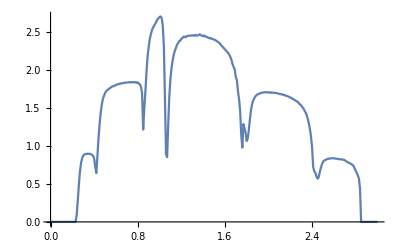

```mathematica
ListPlot[%23,Joined->True]
```

```mathematica
f[M_]:=Table[{ω,Mean[Table[m1[ω,0.5],M]]},{ω,Range[0,1.5,0.01]}]
```

```mathematica
f[50]
```

{{0.,2.79845×10^-7},{0.01,2.60934×10^-7},{0.02,2.61597×10^-7},{0.03,2.73045×10^-7},{0.04,2.80406×10^-7},{0.05,2.87985×10^-7},{0.06,3.01303×10^-7},{0.07,3.10793×10^-7},{0.08,3.20402×10^-7},{0.09,3.49609×10^-7},{0.1,3.55571×10^-7},{0.11,3.97311×10^-7},{0.12,3.87144×10^-7},{0.13,4.75039×10^-7},{0.14,5.69003×10^-7},{0.15,6.27586×10^-7},{0.16,7.33411×10^-7},{0.17,9.01531×10^-7},{0.18,1.23003×10^-6},{0.19,1.63057×10^-6},{0.2,2.49738×10^-6},{0.21,4.43446×10^-6},{0.22,0.0000115686},{0.23,0.000100916},{0.24,0.289901},{0.25,0.615309},{0.26,0.767658},{0.27,0.804617},{0.28,0.833431},{0.29,0.87251},{0.3,0.888414},{0.31,0.872122},{0.32,0.892786},{0.33,0.903183},{0.34,0.919283},{0.35,0.908796},{0.36,0.93033},{0.37,0.907021},{0.38,0.921137},{0.39,0.901577},{0.4,0.904624},{0.41,0.853672},{0.42,0.705195},{0.43,0.961159},{0.44,1.20275},{0.45,1.35144},{0.46,1.50184},{0.47,1.56188},{0.48,1.63666},{0.49,1.67231},{0.5,1.66759},{0.51,1.71167},{0.52,1.70693},{0.53,1.73185},{0.54,1.74067},{0.55,1.75096},{0.56,1.73856},{0.57,1.75683},{0.58,1.78387},{0.59,1.73866},{0.6,1.79855},{0.61,1.80959},{0.62,1.80998},{0.63,1.79823},{0.64,1.79876},{0.65,1.81777},{0.66,1.79425},{0.67,1.7881},{0.68,1.83317},{0.69,1.80609},{0.7,1.8235},{0.71,1.83039},{0.72,1.82822},{0.73,1.83687},{0.74,1.84872},{0.75,1.81853},{0.76,1.82383},{0.77,1.82941},{0.78,1.84811},{0.79,1.84937},{0.8,1.85073},{0.81,1.85902},{0.82,1.85935},{0.83,1.8433},{0.84,1.82679},{0.85,1.00054},{0.86,1.49763},{0.87,1.94921},{0.88,2.08218},{0.89,2.16235},{0.9,2.28674},{0.91,2.40059},{0.92,2.4116},{0.93,2.4633},{0.94,2.47237},{0.95,2.52187},{0.96,2.62056},{0.97,2.58736},{0.98,2.65872},{0.99,2.64137},{1.,2.63612},{1.01,2.64756},{1.02,2.65165},{1.03,2.56627},{1.04,2.22834},{1.05,1.47843},{1.06,0.712636},{1.07,0.715003},{1.08,1.18067},{1.09,1.59049},{1.1,1.80786},{1.11,1.90781},{1.12,1.97197},{1.13,2.15369},{1.14,2.09685},{1.15,2.18388},{1.16,2.26428},{1.17,2.29812},{1.18,2.35154},{1.19,2.29644},{1.2,2.35896},{1.21,2.34228},{1.22,2.33127},{1.23,2.41846},{1.24,2.35579},{1.25,2.39893},{1.26,2.39829},{1.27,2.39308},{1.28,2.39824},{1.29,2.38388},{1.3,2.41118},{1.31,2.3685},{1.32,2.40551},{1.33,2.37656},{1.34,2.36681},{1.35,2.40148},{1.36,2.43392},{1.37,2.44915},{1.38,2.38267},{1.39,2.38355},{1.4,2.43611},{1.41,2.38711},{1.42,2.42711},{1.43,2.41917},{1.44,2.41814},{1.45,2.3506},{1.46,2.35861},{1.47,2.32694},{1.48,2.37145},{1.49,2.3433},{1.5,2.36343}}

```mathematica
f[100]
```

{{0.,2.76979×10^-7},{0.01,2.66544×10^-7},{0.02,2.70461×10^-7},{0.03,2.69862×10^-7},{0.04,2.74164×10^-7},{0.05,2.89129×10^-7},{0.06,3.01777×10^-7},{0.07,3.09272×10^-7},{0.08,3.25547×10^-7},{0.09,3.44897×10^-7},{0.1,3.66078×10^-7},{0.11,3.76033×10^-7},{0.12,4.39274×10^-7},{0.13,4.78453×10^-7},{0.14,5.49288×10^-7},{0.15,6.31901×10^-7},{0.16,7.43392×10^-7},{0.17,9.34325×10^-7},{0.18,1.14857×10^-6},{0.19,1.64597×10^-6},{0.2,2.51144×10^-6},{0.21,4.48728×10^-6},{0.22,0.0000116259},{0.23,0.000096167},{0.24,0.339142},{0.25,0.665655},{0.26,0.794119},{0.27,0.843131},{0.28,0.876435},{0.29,0.871231},{0.3,0.872181},{0.31,0.910025},{0.32,0.904145},{0.33,0.890937},{0.34,0.923836},{0.35,0.916067},{0.36,0.914735},{0.37,0.917132},{0.38,0.912414},{0.39,0.919772},{0.4,0.908967},{0.41,0.831627},{0.42,0.734173},{0.43,0.970762},{0.44,1.25932},{0.45,1.42915},{0.46,1.51554},{0.47,1.54672},{0.48,1.62983},{0.49,1.64796},{0.5,1.68698},{0.51,1.67687},{0.52,1.70577},{0.53,1.74267},{0.54,1.74641},{0.55,1.74553},{0.56,1.74915},{0.57,1.77876},{0.58,1.76506},{0.59,1.74304},{0.6,1.7775},{0.61,1.79799},{0.62,1.81882},{0.63,1.80068},{0.64,1.78971},{0.65,1.81127},{0.66,1.81282},{0.67,1.8203},{0.68,1.8055},{0.69,1.82477},{0.7,1.81287},{0.71,1.81151},{0.72,1.81921},{0.73,1.83778},{0.74,1.81604},{0.75,1.83962},{0.76,1.84164},{0.77,1.83189},{0.78,1.84268},{0.79,1.84727},{0.8,1.84326},{0.81,1.84374},{0.82,1.85353},{0.83,1.84496},{0.84,1.812},{0.85,1.03378},{0.86,1.43472},{0.87,1.82747},{0.88,2.11072},{0.89,2.21021},{0.9,2.32243},{0.91,2.3613},{0.92,2.42673},{0.93,2.5147},{0.94,2.52518},{0.95,2.56996},{0.96,2.55697},{0.97,2.61723},{0.98,2.64568},{0.99,2.60108},{1.,2.67321},{1.01,2.64197},{1.02,2.6334},{1.03,2.51585},{1.04,2.22825},{1.05,1.50848},{1.06,0.830376},{1.07,0.766829},{1.08,1.23648},{1.09,1.52908},{1.1,1.78288},{1.11,1.96213},{1.12,2.05855},{1.13,2.08855},{1.14,2.16089},{1.15,2.20256},{1.16,2.2658},{1.17,2.29464},{1.18,2.32473},{1.19,2.39423},{1.2,2.33076},{1.21,2.35832},{1.22,2.35803},{1.23,2.36457},{1.24,2.36901},{1.25,2.35339},{1.26,2.42667},{1.27,2.41635},{1.28,2.40104},{1.29,2.39851},{1.3,2.40142},{1.31,2.39484},{1.32,2.38148},{1.33,2.39465},{1.34,2.40698},{1.35,2.38723},{1.36,2.40115},{1.37,2.39156},{1.38,2.42779},{1.39,2.38996},{1.4,2.37397},{1.41,2.3994},{1.42,2.35929},{1.43,2.40382},{1.44,2.4022},{1.45,2.35689},{1.46,2.38912},{1.47,2.32461},{1.48,2.37394},{1.49,2.31404},{1.5,2.33145}}

```mathematica
f[200]
```

{{0.,2.76699×10^-7},{0.01,2.57651×10^-7},{0.02,2.61658×10^-7},{0.03,2.70708×10^-7},{0.04,2.79532×10^-7},{0.05,2.85935×10^-7},{0.06,2.95031×10^-7},{0.07,3.09139×10^-7},{0.08,3.17647×10^-7},{0.09,3.42062×10^-7},{0.1,3.71007×10^-7},{0.11,3.95274×10^-7},{0.12,4.43064×10^-7},{0.13,4.84335×10^-7},{0.14,5.47779×10^-7},{0.15,6.42913×10^-7},{0.16,7.59904×10^-7},{0.17,9.39055×10^-7},{0.18,1.20162×10^-6},{0.19,1.65509×10^-6},{0.2,2.52171×10^-6},{0.21,4.63304×10^-6},{0.22,0.0000116134},{0.23,0.0000925212},{0.24,0.358737},{0.25,0.645128},{0.26,0.761975},{0.27,0.819382},{0.28,0.849249},{0.29,0.8679},{0.3,0.88332},{0.31,0.891303},{0.32,0.896374},{0.33,0.901234},{0.34,0.913596},{0.35,0.908958},{0.36,0.921551},{0.37,0.911739},{0.38,0.919339},{0.39,0.920453},{0.4,0.908123},{0.41,0.824496},{0.42,0.804728},{0.43,1.03414},{0.44,1.27307},{0.45,1.42024},{0.46,1.55492},{0.47,1.56136},{0.48,1.61323},{0.49,1.62485},{0.5,1.67639},{0.51,1.70267},{0.52,1.71024},{0.53,1.71876},{0.54,1.74879},{0.55,1.73519},{0.56,1.76351},{0.57,1.75055},{0.58,1.77087},{0.59,1.77066},{0.6,1.78089},{0.61,1.79854},{0.62,1.79918},{0.63,1.8055},{0.64,1.80628},{0.65,1.80392},{0.66,1.81448},{0.67,1.81786},{0.68,1.81545},{0.69,1.81907},{0.7,1.82719},{0.71,1.82594},{0.72,1.81957},{0.73,1.84122},{0.74,1.8391},{0.75,1.82514},{0.76,1.83987},{0.77,1.83555},{0.78,1.82968},{0.79,1.84125},{0.8,1.84081},{0.81,1.85463},{0.82,1.84423},{0.83,1.85078},{0.84,1.82242},{0.85,1.02566},{0.86,1.35715},{0.87,1.80808},{0.88,2.05991},{0.89,2.19701},{0.9,2.29799},{0.91,2.40321},{0.92,2.45869},{0.93,2.47706},{0.94,2.51966},{0.95,2.55294},{0.96,2.56969},{0.97,2.60986},{0.98,2.63168},{0.99,2.65366},{1.,2.65338},{1.01,2.68428},{1.02,2.63841},{1.03,2.53432},{1.04,2.21692},{1.05,1.49516},{1.06,0.75644},{1.07,0.808974},{1.08,1.24027},{1.09,1.55716},{1.1,1.7621},{1.11,1.96481},{1.12,2.02383},{1.13,2.10069},{1.14,2.16755},{1.15,2.22703},{1.16,2.25748},{1.17,2.26687},{1.18,2.31682},{1.19,2.29352},{1.2,2.30859},{1.21,2.33505},{1.22,2.36966},{1.23,2.36502},{1.24,2.35962},{1.25,2.38154},{1.26,2.39985},{1.27,2.38835},{1.28,2.37264},{1.29,2.40547},{1.3,2.40518},{1.31,2.38891},{1.32,2.3813},{1.33,2.417},{1.34,2.39861},{1.35,2.40242},{1.36,2.41515},{1.37,2.43357},{1.38,2.39909},{1.39,2.38233},{1.4,2.41015},{1.41,2.38856},{1.42,2.36143},{1.43,2.38833},{1.44,2.37013},{1.45,2.39044},{1.46,2.3437},{1.47,2.36616},{1.48,2.36029},{1.49,2.34288},{1.5,2.34162}}

```mathematica
f[400]
```

{{0.,2.76456×10^-7},{0.01,2.56284×10^-7},{0.02,2.67562×10^-7},{0.03,2.66539×10^-7},{0.04,2.75166×10^-7},{0.05,2.87973×10^-7},{0.06,3.00255×10^-7},{0.07,3.09544×10^-7},{0.08,3.25151×10^-7},{0.09,3.39033×10^-7},{0.1,3.61128×10^-7},{0.11,3.86287×10^-7},{0.12,4.31006×10^-7},{0.13,4.74788×10^-7},{0.14,5.41855×10^-7},{0.15,6.36156×10^-7},{0.16,7.55993×10^-7},{0.17,9.3359×10^-7},{0.18,1.20033×10^-6},{0.19,1.66686×10^-6},{0.2,2.45861×10^-6},{0.21,4.58051×10^-6},{0.22,0.0000115633},{0.23,0.0000974635},{0.24,0.362939},{0.25,0.650762},{0.26,0.758243},{0.27,0.828548},{0.28,0.836688},{0.29,0.867916},{0.3,0.878085},{0.31,0.893419},{0.32,0.90088},{0.33,0.914327},{0.34,0.912046},{0.35,0.912253},{0.36,0.912659},{0.37,0.912229},{0.38,0.917163},{0.39,0.912499},{0.4,0.907175},{0.41,0.842112},{0.42,0.821627},{0.43,0.983014},{0.44,1.31003},{0.45,1.41153},{0.46,1.50402},{0.47,1.56491},{0.48,1.62568},{0.49,1.66301},{0.5,1.69189},{0.51,1.70904},{0.52,1.71605},{0.53,1.72374},{0.54,1.74168},{0.55,1.74528},{0.56,1.76415},{0.57,1.76897},{0.58,1.78163},{0.59,1.78325},{0.6,1.78441},{0.61,1.79311},{0.62,1.79249},{0.63,1.79952},{0.64,1.81022},{0.65,1.79156},{0.66,1.80569},{0.67,1.81564},{0.68,1.81759},{0.69,1.81344},{0.7,1.82112},{0.71,1.82939},{0.72,1.83495},{0.73,1.83502},{0.74,1.82331},{0.75,1.83603},{0.76,1.83669},{0.77,1.83424},{0.78,1.83943},{0.79,1.84021},{0.8,1.84603},{0.81,1.84708},{0.82,1.84472},{0.83,1.85023},{0.84,1.81794},{0.85,1.05126},{0.86,1.40244},{0.87,1.84269},{0.88,2.07538},{0.89,2.20158},{0.9,2.30504},{0.91,2.38824},{0.92,2.43847},{0.93,2.48669},{0.94,2.52187},{0.95,2.53767},{0.96,2.57096},{0.97,2.6069},{0.98,2.63068},{0.99,2.63977},{1.,2.65762},{1.01,2.65532},{1.02,2.63009},{1.03,2.50183},{1.04,2.21952},{1.05,1.5023},{1.06,0.757775},{1.07,0.755016},{1.08,1.2036},{1.09,1.55896},{1.1,1.77166},{1.11,1.94129},{1.12,2.04854},{1.13,2.10174},{1.14,2.16491},{1.15,2.2284},{1.16,2.26771},{1.17,2.26886},{1.18,2.30188},{1.19,2.31876},{1.2,2.32745},{1.21,2.35047},{1.22,2.36758},{1.23,2.37704},{1.24,2.37691},{1.25,2.38341},{1.26,2.376},{1.27,2.38251},{1.28,2.39},{1.29,2.38193},{1.3,2.41537},{1.31,2.41256},{1.32,2.39469},{1.33,2.4011},{1.34,2.38959},{1.35,2.40049},{1.36,2.39447},{1.37,2.40779},{1.38,2.40511},{1.39,2.39332},{1.4,2.38545},{1.41,2.38201},{1.42,2.39509},{1.43,2.38521},{1.44,2.37584},{1.45,2.35854},{1.46,2.35636},{1.47,2.36575},{1.48,2.36022},{1.49,2.35203},{1.5,2.35451}}

```mathematica
f[800]
```

{{0.,2.7658×10^-7},{0.01,2.63292×10^-7},{0.02,2.61406×10^-7},{0.03,2.72158×10^-7},{0.04,2.79709×10^-7},{0.05,2.83978×10^-7},{0.06,2.97884×10^-7},{0.07,3.09034×10^-7},{0.08,3.20913×10^-7},{0.09,3.38698×10^-7},{0.1,3.6447×10^-7},{0.11,3.95768×10^-7},{0.12,4.28559×10^-7},{0.13,4.73713×10^-7},{0.14,5.43802×10^-7},{0.15,6.28955×10^-7},{0.16,7.50259×10^-7},{0.17,9.26169×10^-7},{0.18,1.19614×10^-6},{0.19,1.66239×10^-6},{0.2,2.50116×10^-6},{0.21,4.5635×10^-6},{0.22,0.0000117462},{0.23,0.000096214},{0.24,0.35609},{0.25,0.661309},{0.26,0.758968},{0.27,0.823594},{0.28,0.844622},{0.29,0.862549},{0.3,0.876822},{0.31,0.895473},{0.32,0.903581},{0.33,0.909037},{0.34,0.909864},{0.35,0.912053},{0.36,0.91409},{0.37,0.916567},{0.38,0.913569},{0.39,0.912081},{0.4,0.907242},{0.41,0.836628},{0.42,0.768922},{0.43,1.03552},{0.44,1.26357},{0.45,1.41899},{0.46,1.50887},{0.47,1.57947},{0.48,1.60972},{0.49,1.63781},{0.5,1.67825},{0.51,1.70512},{0.52,1.71362},{0.53,1.714},{0.54,1.73448},{0.55,1.74651},{0.56,1.7562},{0.57,1.75787},{0.58,1.77507},{0.59,1.77755},{0.6,1.78354},{0.61,1.7944},{0.62,1.79241},{0.63,1.80124},{0.64,1.80932},{0.65,1.79743},{0.66,1.80869},{0.67,1.8199},{0.68,1.81708},{0.69,1.81309},{0.7,1.82214},{0.71,1.83061},{0.72,1.82773},{0.73,1.83269},{0.74,1.83504},{0.75,1.82942},{0.76,1.82978},{0.77,1.83265},{0.78,1.8417},{0.79,1.83988},{0.8,1.8467},{0.81,1.84562},{0.82,1.85152},{0.83,1.84681},{0.84,1.81238},{0.85,1.06563},{0.86,1.44205},{0.87,1.82431},{0.88,2.06537},{0.89,2.20725},{0.9,2.28823},{0.91,2.35529},{0.92,2.44428},{0.93,2.49247},{0.94,2.52541},{0.95,2.53461},{0.96,2.57461},{0.97,2.60072},{0.98,2.63046},{0.99,2.62314},{1.,2.65171},{1.01,2.65367},{1.02,2.62968},{1.03,2.52248},{1.04,2.22293},{1.05,1.49639},{1.06,0.77811},{1.07,0.774769},{1.08,1.18906},{1.09,1.56284},{1.1,1.76496},{1.11,1.91233},{1.12,2.03861},{1.13,2.11179},{1.14,2.17475},{1.15,2.20883},{1.16,2.25255},{1.17,2.2661},{1.18,2.31014},{1.19,2.32143},{1.2,2.34995},{1.21,2.35924},{1.22,2.37542},{1.23,2.37843},{1.24,2.35737},{1.25,2.38575},{1.26,2.39227},{1.27,2.39318},{1.28,2.38602},{1.29,2.38109},{1.3,2.40543},{1.31,2.40824},{1.32,2.38542},{1.33,2.40752},{1.34,2.39993},{1.35,2.42028},{1.36,2.40302},{1.37,2.40108},{1.38,2.40656},{1.39,2.38215},{1.4,2.38329},{1.41,2.39252},{1.42,2.37591},{1.43,2.37569},{1.44,2.38897},{1.45,2.35755},{1.46,2.34888},{1.47,2.36954},{1.48,2.34682},{1.49,2.35406},{1.5,2.35043}}

```mathematica
f[1600]
```

{{0.,2.77172×10^-7},{0.01,2.61336×10^-7},{0.02,2.64289×10^-7},{0.03,2.72259×10^-7},{0.04,2.75392×10^-7},{0.05,2.84347×10^-7},{0.06,2.95419×10^-7},{0.07,3.07048×10^-7},{0.08,3.21784×10^-7},{0.09,3.41133×10^-7},{0.1,3.62328×10^-7},{0.11,3.88153×10^-7},{0.12,4.30041×10^-7},{0.13,4.79969×10^-7},{0.14,5.42078×10^-7},{0.15,6.3659×10^-7},{0.16,7.55323×10^-7},{0.17,9.24456×10^-7},{0.18,1.19362×10^-6},{0.19,1.65262×10^-6},{0.2,2.50087×10^-6},{0.21,4.51598×10^-6},{0.22,0.0000117159},{0.23,0.0000956757},{0.24,0.355492},{0.25,0.663007},{0.26,0.770422},{0.27,0.818093},{0.28,0.846223},{0.29,0.8619},{0.3,0.880726},{0.31,0.891834},{0.32,0.90279},{0.33,0.905411},{0.34,0.913235},{0.35,0.913009},{0.36,0.914516},{0.37,0.914113},{0.38,0.916298},{0.39,0.915501},{0.4,0.903435},{0.41,0.835683},{0.42,0.792531},{0.43,1.02953},{0.44,1.28202},{0.45,1.41794},{0.46,1.50434},{0.47,1.57834},{0.48,1.60806},{0.49,1.65691},{0.5,1.66904},{0.51,1.69711},{0.52,1.71292},{0.53,1.72469},{0.54,1.73474},{0.55,1.74667},{0.56,1.75578},{0.57,1.7676},{0.58,1.77485},{0.59,1.77186},{0.6,1.78228},{0.61,1.7925},{0.62,1.78983},{0.63,1.79933},{0.64,1.80665},{0.65,1.80708},{0.66,1.81205},{0.67,1.81622},{0.68,1.81289},{0.69,1.81893},{0.7,1.82202},{0.71,1.82445},{0.72,1.82503},{0.73,1.83095},{0.74,1.83517},{0.75,1.82812},{0.76,1.83654},{0.77,1.83654},{0.78,1.84308},{0.79,1.84153},{0.8,1.84906},{0.81,1.84171},{0.82,1.8495},{0.83,1.84671},{0.84,1.82043},{0.85,1.07947},{0.86,1.42062},{0.87,1.82024},{0.88,2.06028},{0.89,2.21508},{0.9,2.29468},{0.91,2.38999},{0.92,2.44476},{0.93,2.48018},{0.94,2.51585},{0.95,2.55202},{0.96,2.57668},{0.97,2.59258},{0.98,2.636},{0.99,2.64242},{1.,2.653},{1.01,2.66635},{1.02,2.63079},{1.03,2.52506},{1.04,2.21244},{1.05,1.53601},{1.06,0.772458},{1.07,0.782703},{1.08,1.19178},{1.09,1.53618},{1.1,1.79208},{1.11,1.92843},{1.12,2.02343},{1.13,2.1222},{1.14,2.15766},{1.15,2.2129},{1.16,2.25729},{1.17,2.28108},{1.18,2.30958},{1.19,2.32355},{1.2,2.33657},{1.21,2.34418},{1.22,2.36661},{1.23,2.3887},{1.24,2.36945},{1.25,2.38553},{1.26,2.387},{1.27,2.38162},{1.28,2.39605},{1.29,2.38298},{1.3,2.40414},{1.31,2.40311},{1.32,2.39992},{1.33,2.41389},{1.34,2.39405},{1.35,2.41382},{1.36,2.40344},{1.37,2.40246},{1.38,2.40026},{1.39,2.38515},{1.4,2.38566},{1.41,2.38916},{1.42,2.3739},{1.43,2.38469},{1.44,2.38306},{1.45,2.37147},{1.46,2.36416},{1.47,2.3566},{1.48,2.35813},{1.49,2.35205},{1.5,2.35894}}

```mathematica
Export["/home/shardulmukim/PhD/fwi/7AGNR/50unitcells/errorm1/m50.dat",%21]
Export["/home/shardulmukim/PhD/fwi/7AGNR/50unitcells/errorm1/m100.dat",%22]
Export["/home/shardulmukim/PhD/fwi/7AGNR/50unitcells/errorm1/m200.dat",%23]
Export["/home/shardulmukim/PhD/fwi/7AGNR/50unitcells/errorm1/m400.dat",%24]
Export["/home/shardulmukim/PhD/fwi/7AGNR/50unitcells/errorm1/m800.dat",%25]
Export["/home/shardulmukim/PhD/fwi/7AGNR/50unitcells/errorm1/m1600.dat",%26]
```

/home/shardulmukim/PhD/fwi/7AGNR/50unitcells/errorm1/m50.dat

/home/shardulmukim/PhD/fwi/7AGNR/50unitcells/errorm1/m100.dat

/home/shardulmukim/PhD/fwi/7AGNR/50unitcells/errorm1/m200.dat

/home/shardulmukim/PhD/fwi/7AGNR/50unitcells/errorm1/m400.dat

/home/shardulmukim/PhD/fwi/7AGNR/50unitcells/errorm1/m800.dat

/home/shardulmukim/PhD/fwi/7AGNR/50unitcells/errorm1/m1600.dat